Units used: GeV for masses, ps for lifetimes, cm for distances

```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookSave[];
```

```mathematica
SetDirectory[ NotebookDirectory[]]
```

/home/stasya/prj/Rare_B_decays

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

### Belle II parameters

```mathematica
τB=1.638;(*ps*)
ΓtotalB=6.582*10^-25/(10^-12 τB);(*GeV*)
cτB=3 10^10 10^-12 τB(*in cm*);
```

```mathematica
τK=10^12 1.238*10^-8;(*ps*)
ΓtotalK=6.582*10^-25/(10^-12 τK);(*GeV*)
cτK=3 10^10 10^-12 τK(*in cm*);
```

All γβB is now actually γB

```mathematica
100 fb^-1
```

```mathematica
Belle2params={γβB:>1.03029,RKLM:>300,θKLMMin:>40 Degree, θKLMMax:>129 Degree,RCDC:>162,θCDCMin:>17 Degree, θCDCMax:>150 Degree,dres:>10^-4 500,NBBBelleII:>5*10^10/500};
Belleparams={γβB:>1.08657,RCDC:>86.3,θCDCMin:>17 Degree, θCDCMax:>150 Degree,dres:>10^-4 500,NBBBelle:>5*10^10/50};
```

```mathematica
Sin[150 Degree//N]
```

0.5

```mathematica
162/0.3
```

540.

### Init

```mathematica
(* Formfactor definition and values from [1811.00983] *)
```

```mathematica
tplus[mK_]:=(mB+mK)^2;
tminus[mK_]:=(mB-mK)^2;
tzero[mK_]:=tplus[mK](1-Sqrt[1-tminus[mK]/tplus[mK]]);
```

```mathematica
zz[t_,mK_]:=(Sqrt[tplus[mK]-t]-Sqrt[tplus[mK]-tzero[mK]])/(Sqrt[tplus[mK]-t]+Sqrt[tplus[mK]-tzero[mK]]);
```

```mathematica
FF[q.b2_,x_,mK_]:=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](zz[q.b2,mK]-zz[0,mK])^k,{k,0,2}]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
V0AB[q.b2_,F0_,aAB_,bAB_]:= F0/(1-aAB (q.b2)/mB^2+bAB((q.b2)/mB^2)^2)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
(* we need f0 and f+ only for the B->K pseudoscalar decay, but A0 for B->K^* vector decays for different K^* masses, so we explicitly have to add mP (or mK^*) here *)
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[α, 0,Azero]:>0.343,Subscript[α, 1,Azero]:>-1.130,Subscript[α, 2,Azero]:>2.326,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 ,Subscript[m, R,Azero]:>5.279,F0BS700:>0.46, aS700:>1.6,bS700:>1.35 ,F0BS1430:>0.17, aS1430:>4.4,bS1430:>6.4 ,F0A:>0.22, F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 Degree,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07};
```

```mathematica
V0BK1270func[q.b2_]:=1/1.270(Sin[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]+Cos[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
V0BK1400func[q.b2_]:=1/1.4(Cos[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]-Sin[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
```

```mathematica
formFactors={fplus[q.b2_,F0_,a_,b_]:> V0AB[q.b2,F0,a,b],V0BK1270[q.b2_]:>V0BK1270func[q.b2] ,V0BK1400[q.b2_]:>V0BK1400func[q.b2] , fzero[q.b2_]:> FF[q.b2,fzero,mK],Azero[qsqr_,mP_]:>FF[qsqr,Azero,mP]};
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188,vev:>246.22, mKstarV892:>0.892, mKstarV1410:>1.41, mKstarV1680:>1.72,mKAV1270:>1.27,mKAV1400:>1.4,mKstarS700:>0.7,mKstarS1430:>1.43};

ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

### Geometrical integration over detector

```mathematica
(*γβ[γβParent_,mParent_,mϕ_]:=γβParent mParent/(2 mϕ)/.formFactors/.values/.masses/.couplings/.ckms*)
```

γβParent is actually γBParent

```mathematica
γβ[γParent_,mParent_,mϕ_]:=√(γParent^2 ((mB^2-mK^2+mϕ^2)^2)/(4 mB^2 mϕ^2)-1)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
θminBoost[θmin_,r_,cτ_,γβ_]:=ArcTan[r/(r/Tan[θmin]-γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
θmaxBoost[θmax_,r_,cτ_,γβ_]:=π+ArcTan[-r/(-r/Tan[θmax]+γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
GeomInt[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=1/(4(γβ  cτ)^2)NIntegrate[1/Sin[θ](ⅇ^(-dmin/(Sin[θ] γβ  cτ))(dmin^2+2 γβ  cτ Sin[θ](dmin+γβ  cτ Sin[θ]) )-ⅇ^(-dmax/(Sin[θ] γβ cτ))(dmax^2+2 γβ  cτ Sin[θ](dmax+γβ  cτ Sin[θ]) ))/.formFactors/.values/.masses/.couplings/.ckms,{θ,θmin,θmax}]
```

```mathematica
GeomIntNewPart[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=1/(4(γβ  cτ)^2)NIntegrate[1/Sin[θ](ⅇ^(-dmin/(Sin[θ] γβ  cτ))(dmin^2+2 γβ  cτ Sin[θ](dmin) )-ⅇ^(-dmax/(Sin[θ] γβ cτ))(dmax^2+2 γβ  cτ Sin[θ](dmax) ))/.formFactors/.values/.masses/.couplings/.ckms,{θ,θmin,θmax}]
```

```mathematica
γβϕB[mϕ_]:=γβ[γβB,mB,mϕ]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
GeomIntCDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
GeomIntBelleIICDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=ReplaceAll[Belle2params][HeavisideTheta[Re[RCDC/Tan[θmin]-γβB cτB]]GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms];
```

```mathematica
GeomIntBelleCDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=ReplaceAll[Belleparams][HeavisideTheta[Re[RCDC/Tan[θmin]-γβB cτB]]GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms];
```

```mathematica
expDecay[d_,θ_,mϕ_,α_,BRDM_]:=Exp[-d/(Sin[θ] γβ[γβB,mB,mϕ] cτϕBRDM[mϕ,α,BRDM])]/.HeavisideTheta[0]:>1/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

### Plots/checks

```mathematica
Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[2,10^-5,0],γβϕB[2]]]
```

NIntegrate::inumr: The integrand 1/2 (-ⅇ^(-(137.861 Csc[θ])/cτϕBRDM[2,1/100000,0])+ⅇ^(-(0.0425497 Csc[θ])/cτϕBRDM[2,1/100000,0])) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[1/2 Sin[θ] (ⅇ^(-1/(20 (Sin[θ] 1.1751 cτϕBRDM[2,1/100000,0])))-ⅇ^(-162/(Sin[θ] 1.1751 cτϕBRDM[2,1/100000,0])))/.formFactors/.values/.masses/.couplings/.ckms,{θ,0.296733,2.61807}]

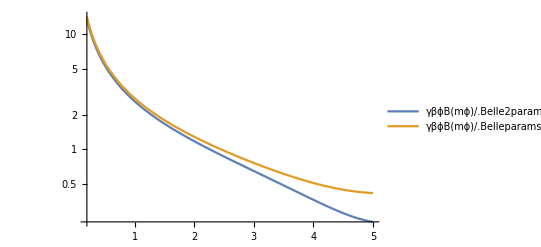

```mathematica
LogPlot[{(γβϕB[mϕ]/.Belle2params),(γβϕB[mϕ]/.Belleparams)},{mϕ,0.2,5}, PlotRange->Full, PlotLegends->"Expressions"]
```

```mathematica
LogPlot[{(cτϕBRDM[mϕ,10^-4,0]γβϕB[mϕ])/.Belle2params},{mϕ,0.2,5}, PlotRange->Full, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
cτϕBRDM[2,10^-4,0]γβϕB[2]/.Belle2params
```

1.1751 cτϕBRDM[2,1/10000,0]

```mathematica
γβϕB[3]/.Belle2params
```

0.647465

```mathematica
γβϕB[5]/.Belle2params
```

0.234171

```mathematica
LogLinearPlot[{(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[0.3,α,0],γβϕB[0.3]]] ),(Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[0.3,α,0],γβϕB[0.3]]])},{α,10^-7,1 10^-1},PlotLegends->"Expressions", PlotRange->Full,FrameLabel->{"α",""}, Frame -> True, PlotLabel->"mS=0.3 GeV"]
```

NIntegrate::inumr: The integrand 1/2 (-ⅇ^(-(9.63257 Csc[θ])/cτϕBRDM[0.3,1.00028×10^-7,0])+ⅇ^(-(0.00558086 Csc[θ])/cτϕBRDM[0.3,1.00028×10^-7,0])) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296756,2.61814}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
LogLinearPlot[{(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belle2params,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[0.3,α,0],γβϕB[0.3]]] ),(Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],B0,B+dres,RCDC,cτϕBRDM[0.3,α,0],γβϕB[0.3]]])},{α,10^-7,1 10^-1},PlotLegends->"Expressions", PlotRange->Full,FrameLabel->{"α",""}, Frame -> True, PlotLabel->"mS=0.3 GeV"]
```

NIntegrate::inumr: The integrand 1/2 (-ⅇ^(-(18.082 Csc[θ])/cτϕBRDM[0.3,1.00028×10^-7,0])+ⅇ^(-(0.00558086 Csc[θ])/cτϕBRDM[0.3,1.00028×10^-7,0])) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

InterpolatingFunction::dmval: Input value {0.30006} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.81101}. NIntegrate obtained -0.233851+0. ⅈ and 0.0754137 for the integral and error estimates.

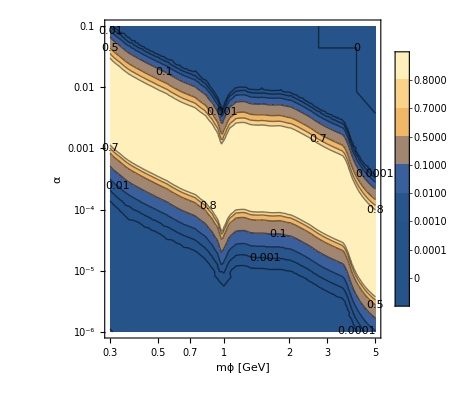

GeomInt_new.png

```mathematica
ContourPlot[(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]] ),{mϕ,0.3,5},{α,10^-6,1 10^-1},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->{0,0.0001,0.001,0.01,0.1,0.5,0.7,0.8,1}]
Export["GeomInt_new.png",%]
```

InterpolatingFunction::dmval: Input value {0.30006} lies outside the range of data in the interpolating function. Extrapolation will be used.

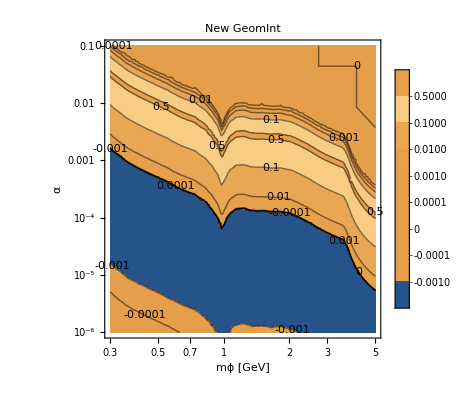

GeomInt_newPart.png

```mathematica
ContourPlot[(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntNewPart[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]] ),{mϕ,0.3,5},{α,10^-6,1 10^-1},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->{-0.001,-0.0001,0,0.0001,0.001,0.01,0.1,0.5,0.7},PlotLabel->"New GeomInt"]
Export["GeomInt_newPart.png",%]
```

InterpolatingFunction::dmval: Input value {4.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

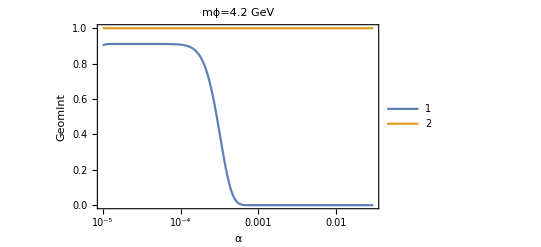

```mathematica
LogLinearPlot[{(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[4.2,α,0],γβϕB[4.2]]] ),1},{α,10^-5,3 10^-2},PlotLegends->Automatic, PlotRange->Full,Frame-> True,FrameLabel->{"α","GeomInt"},PlotLabel->"mϕ=4.2 GeV"]
```

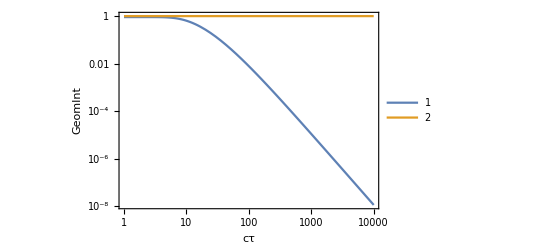

```mathematica
LogLogPlot[{(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕ,γβϕB[0.5]]] ),1},{cτϕ,1,10000},PlotLegends->Automatic, PlotRange->Full,Frame -> True,FrameLabel->{"cτ","GeomInt"}]
```

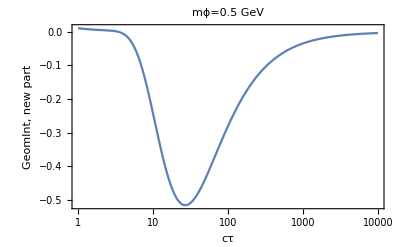

```mathematica
LogLinearPlot[{(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntNewPart[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕ,γβϕB[0.5]]] )},{cτϕ,1,10000},PlotLegends->Automatic, PlotRange->Full,Frame -> True,FrameLabel->{"cτ","GeomInt, new part"},PlotLabel->"mϕ=0.5 GeV"]
```

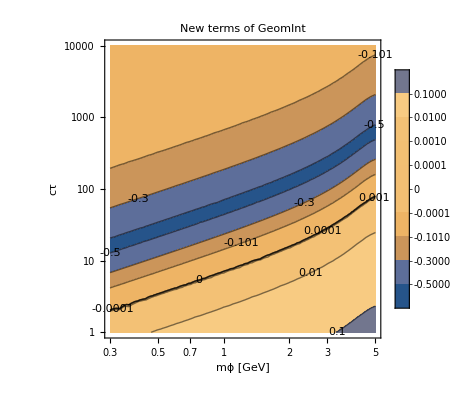

GeomInt_newPart_ctau.png

```mathematica
ContourPlot[(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntNewPart[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕ,γβϕB[mϕ]]] ),{mϕ,0.3,5},{cτϕ,1,10000},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","cτ"},Contours->{-0.5,-0.3,-0.1-0.001,-0.0001,0,0.0001,0.001,0.01,0.1,1},PlotLabel->"New terms of GeomInt"]
Export["GeomInt_newPart_ctau.png",%]
```

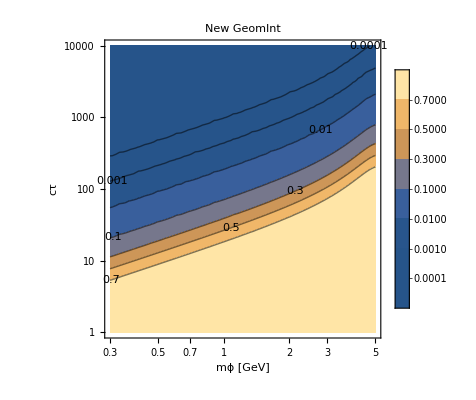

GeomInt_new_ctau.png

```mathematica
ContourPlot[(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕ,γβϕB[mϕ]]] ),{mϕ,0.3,5},{cτϕ,1,10000},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","cτ"},Contours->{0,0.0001,0.001,0.01,0.1,0.3,0.5,0.7,1},PlotLabel->"New GeomInt"]
Export["GeomInt_new_ctau.png",%]
```

Different boost, the rest parameters stay like at Belle

InterpolatingFunction::dmval: Input value {0.30006} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.87597} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45742}. NIntegrate obtained 5.2277×10^-320+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74759}. NIntegrate obtained 2.47×10^-322+0. ⅈ and 0. for the integral and error estimates.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74759}. NIntegrate obtained 1.04×10^-322+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

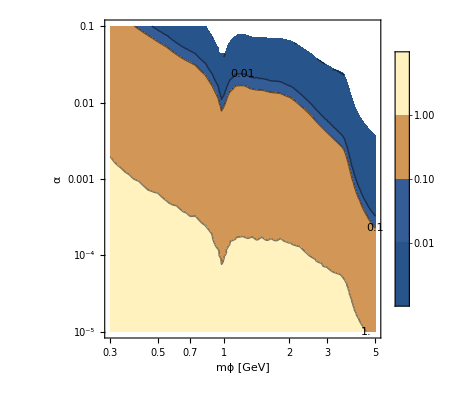

```mathematica
ContourPlot[(Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]] )/(Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]]),{mϕ,0.3,5},{α,10^-5,1 10^-1},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->{0,0.01,0.1,1,2,10,100,1000}]
```

Different RCDC, the rest parameters stay like at Belle II

InterpolatingFunction::dmval: Input value {0.30006} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.9687} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45737}. NIntegrate obtained 5.227×10^-320+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45742}. NIntegrate obtained 5.2277×10^-320+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74754}. NIntegrate obtained 2.47×10^-322+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

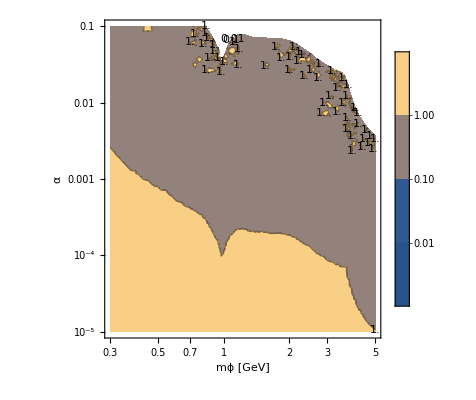

```mathematica
ContourPlot[(Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belle2params,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]] )/(Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomIntCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,0],γβϕB[mϕ]]]),{mϕ,0.3,5},{α,10^-5,1 10^-1},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->{0,0.01,0.1,1,2}]
```

### Γϕ

```mathematica
datapointsππ=ReadList[File["rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

```mathematica
datapointsππ={{0.28001323,5.17024*10^(-10)},{0.27784854,1.0525554*10^(-9)},{0.2877911,1.8218304*10^(-9)},{0.30592537,3.3623317*10^(-9)},{0.33365947,5.277515*10^(-9)},{0.3639078,8.283586*10^(-9)},{0.41079497,1.2181233*10^(-8)},{0.47179008,1.7907567*10^(-8)},{0.5560635,2.7178222*10^(-8)},{0.6442094,4.2615103*10^(-8)},{0.73974603,5.5053757*10^(-8)},{0.8280175,9.213942*10^(-8)},{0.8877805,1.6462049*10^(-7)},{0.9437583,3.1379568*10^(-7)},{0.97783643,7.033213*10^(-7)},{1.002676,3.6842826*10^(-7)},{1.036807,1.5896644*10^(-7)},{1.0629779,7.317836*10^(-8)},{1.108985,3.958082*10^(-8)},{1.1371115,2.0074902*10^(-8)},{1.1865596,1.27616815*10^(-8)},{1.2277195,9.23311*10^(-9)},{1.2817607,8.933028*10^(-9)},{1.3385478,1.08358424*10^(-8)},{1.3852515,9.2141486*10^(-9)},{1.47,4.38*10^(-9)},{1.5,2.5269602*10^(-9)},{1.5614661,4.1001567*10^(-9)},{1.6033295,6.6537464*10^(-9)},{1.6742321,7.566051*10^(-9)},{1.7473112,5.4732547*10^(-9)},{1.8077103,3.5941348*10^(-9)},{1.88713,3.25975*10^(-9)},{1.9999999,3.7056085*10^(-9)}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

```mathematica
datapointsKK={{0.992899,1.39798*10^(-7)},{1.07269,1.07816*10^(-7)},{1.13916,8.87269*10^(-8)},{1.25236,8.04012*10^(-8)},{1.31897,8.56912*10^(-8)},{1.45009,8.02007*10^(-8)},{1.58049,7.26857*10^(-8)}{1.69277,5.42831*10^(-8)},{1.81310,4.18707*10^(-8)},{1.99304,3.44371*10^(-8)}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
ΓϕSM[mϕ_,α_]:=Γϕ[mϕ,mϕ,0,α]/.HeavisideTheta[0]:>1
ΓϕBRDM[mϕ_,α_,BRχ_]:=ΓϕSM[mϕ,α](1+BRχ/(1-BRχ))(*ΓSM+Γχ for given BRχ*)
τϕ[mϕ_,mχ_,ξ_,α_]:=10^12(Γϕ[mϕ,mχ,ξ,α] GevToInverseSec)^-1/.constants (*in psc*)
τϕBRDM[mϕ_,α_,BRχ_]:=10^12(ΓϕBRDM[mϕ,α,BRχ] GevToInverseSec)^-1/.constants (*in psc*)
cτϕBRDM[mϕ_,α_,BRχ_]:=3 10^10 10^-12 τϕBRDM[mϕ,α,BRχ](*in cm*)
cτϕVisible[mϕ_,α_]:=3 10^10(ΓϕSM[mϕ,α] GevToInverseSec)^-1/.constants (*in psc*)
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
Γϕtoττ[mϕ_,α_]:=Γϕf[mϕ,α,mτ]
```

```mathematica
ContourPlot[cτϕBRDM[m,α,0],{m,0.2,4},{α, 10^-6,0.001},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Black},Contours->{1,10,100,1000,10000},ContourLabels->All, PlotLegends->Automatic,PlotRange->All]
Export["ctau.png",%]
```

InterpolatingFunction::dmval: Input value {0.200271} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.471429} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

ctau.png

### B^+ -> K^+pseudoscalar μμ,ππ,KK,ττ width

```mathematica
(* The interesting part about the B->Kμμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKPμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKPϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPττBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPππBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPKKBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (MB+MS)^2 √((mB^2-(mK-mϕ)^2)  (mB^2-(mK+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/((MW^2-MT^2)^6))((mB^2-mK^2)^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2)HeavisideTheta[mB-(mK+mϕ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKPμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKPττBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPττBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKPππBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPππBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKPKKBRDM[mϕ_,α_,BRχ_]:=ΓBtoKPKKBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

#### SM contributions

```mathematica
BRBtoKμμSM=1.9 10^-6;
```

#### Checks/plots

```mathematica
LogLinearPlot[BRBtoKμμBRDMKLM[4,α,0],{α,10^-6,10^0},PlotRange->Full]
```

-Graphics-

### B^+ -> K^*scalar μμ,ππ,KK,ττ width

```mathematica
(* The interesting part about the B->Kμμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKstarSμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSττBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSππBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSKKBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSϕGen[mϕ_,α_,mKscalar_,F0_,a_,b_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fplus[mϕ^2,F0,a,b]^2 (MB+MS)^2 √((mB^2-(mKscalar-mϕ)^2)  (mB^2-(mKscalar+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/((MW^2-MT^2)^6))((mB^2-mKscalar^2-mϕ^2)^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB+MS)^2)HeavisideTheta[mB-(mKscalar+mϕ)]

ΓBtoKstarSϕ[mϕ_,α_]:=(ΓBtoKstarSϕGen[mϕ,α,mKstarS700,F0BS700,aS700,bS700]+ΓBtoKstarSϕGen[mϕ,α,mKstarS1430,F0BS1430,aS1430,bS1430])/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKstarSμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKstarSττBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSττBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKstarSππBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSππBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKstarSKKBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarSKKBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

#### SM contributions

```mathematica
BRBtoKμμSM=1.9 10^-6;
```

#### Checks/plots

```mathematica
LogLinearPlot[BRBtoKμμBRDMKLM[4,α,0],{α,10^-6,10^0},PlotRange->Full]
```

-Graphics-

### B -> K^* vector μμ,ππ,KK,ττ width

```mathematica
(* The interesting part about the B->K^*μμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKstarVμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVττBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVππBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVKKBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarVϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVϕGen[mϕ_,α_,mKstar_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 Azero[mϕ^2,mKstar]^2 (MB+MS)^2 √((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/((MW^2-MT^2)^6))((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))/(4194304 π^5 mB^3 MW^6 SW^6 (MB+MS)^2)HeavisideTheta[mB-(mKstar+mϕ)]/.formFactors/.values/.masses/.couplings/.ckms
ΓBtoKstarVϕ[mϕ_,α_]:=(ΓBtoKstarVϕGen[mϕ,α,mKstarV892]+ΓBtoKstarVϕGen[mϕ,α,mKstarV1410]+ΓBtoKstarVϕGen[mϕ,α,mKstarV1680])/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKstarVμμBRDM[mϕ_,α_,BRχ_]=ΓBtoKstarVμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKstarVττBRDM[mϕ_,α_,BRχ_]=ΓBtoKstarVττBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKstarVππBRDM[mϕ_,α_,BRχ_]=ΓBtoKstarVππBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKstarVKKBRDM[mϕ_,α_,BRχ_]=ΓBtoKstarVKKBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
Xsvglplot[10^-3,0]
```

Xsvglplot[1/1000,0]

```mathematica
BrXsvglplot[10^-3,0]
```

BrXsvglplot[1/1000,0]

#### SM contributions

#### Checks/plots

```mathematica
LogLinearPlot[BRBtoKμμBRDMKLM[4,α,0],{α,10^-6,10^0},PlotRange->Full]
```

-Graphics-

### B -> K axialvector μμ,ππ,KK,ττ width

```mathematica
(* The interesting part about the B->K^*μμ - process is in the resonance, so that we can take *)
```

```mathematica
ΓBtoKAVμμ[mϕ_,mχ_,ξ_,α_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/Γϕ[mϕ,mχ,ξ,α]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVττBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVππBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVKKBRDM[mϕ_,α_,BRχ_]:=ΓBtoKstarAVϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVϕGen[mϕ_,α_,mKstar_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 V0[mϕ^2]^2 (MB+MS)^2 √((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)/((MW^2-MT^2)^6))((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2)HeavisideTheta[mB-(mKstar+mϕ)]
ΓBtoKstarAVϕ[mϕ_,α_]:=((ΓBtoKAVϕGen[mϕ,α,mKAV1270]/.V0-> V0BK1270)+(ΓBtoKAVϕGen[mϕ,α,mKAV1400]/.V0-> V0BK1400))/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVμμBRDM[mϕ_,α_,BRχ_]=ΓBtoKAVμμBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVττBRDM[mϕ_,α_,BRχ_]=ΓBtoKAVττBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVππBRDM[mϕ_,α_,BRχ_]=ΓBtoKAVππBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVKKBRDM[mϕ_,α_,BRχ_]=ΓBtoKAVKKBRDM[mϕ,α,BRχ]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

#### SM contributions

#### Checks/plots

```mathematica
LogLinearPlot[BRBtoKμμBRDMKLM[4,α,0],{α,10^-6,10^0},PlotRange->Full]
```

-Graphics-

### K^+vs K^* plots

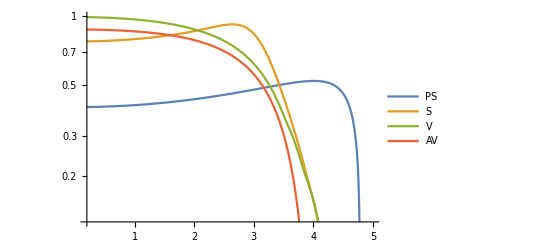

```mathematica
LogPlot[{(ΓBtoKPϕ[mϕ,10^-4]/(ΓtotalB Sin[10^-4]^2))/.formFactors/.values/.masses/.couplings/.ckms,(ΓBtoKstarSϕ[mϕ,10^-4]/(ΓtotalB Sin[10^-4]^2))/.formFactors/.values/.masses/.couplings/.ckms,(ΓBtoKstarVϕ[mϕ,10^-4]/(ΓtotalB Sin[10^-4]^2))/.formFactors/.values/.masses/.couplings/.ckms,(ΓBtoKstarAVϕ[mϕ,10^-2]/(ΓtotalB Sin[10^-2]^2))/.formFactors/.values/.masses/.couplings/.ckms},{mϕ,0.2,5},PlotLegends->{"PS","S","V","AV"}]
```

### Xs width

```mathematica
ΓBtoXsμμBRDM[mϕ_,α_,BRχ_]:=ΓBtoXsϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoXsππBRDM[mϕ_,α_,BRχ_]:=ΓBtoXsϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,BRχ]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoXsϕ[mϕ_,α_]:=((Sin[α]mb)/vev (3 √2 GF mt^2 Conjugate[Vts]Vtb)/(15 π^2))^2((mB^2-mϕ^2)^2)/(32 π mB^3)
```

```mathematica
BrBtoXsμμBRDM[mϕ_,α_,BRχ_]=ΓBtoXsμμBRDM[mϕ,α,BRχ]/ΓtotalB;
```

```mathematica
BrBtoXsππBRDM[mϕ_,α_,BRχ_]=ΓBtoXsππBRDM[mϕ,α,BRχ]/ΓtotalB;
```

InterpolatingFunction::dmval: Input value {0.010035} lies outside the range of data in the interpolating function. Extrapolation will be used.

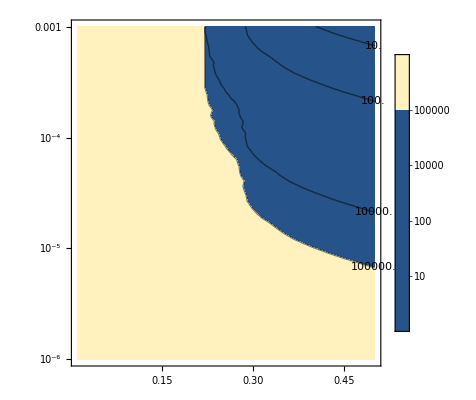

```mathematica
ContourPlot[γβ[γβB,MB,mϕ]cτϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params,{mϕ,0.01,0.5},{α,10^-6,1 10^-3},Contours-> {10,100,10^4,10^5},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{None,"Log"}]
```

InterpolatingFunction::dmval: Input value {0.30006} lies outside the range of data in the interpolating function. Extrapolation will be used.

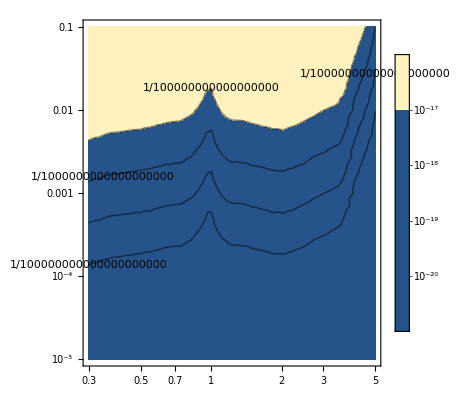

```mathematica
ContourPlot[ΓBtoXsμμBRDM[mϕ,α,0]/.{qH.b2:>mϕ^2}/.formFactors/.values/.masses/.couplings/.ckms,{mϕ,0.3,5},{α,10^-5,1 10^-1},Contours-> {10^-20,10^-19,10^-18,10^-17},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"}]
```

InterpolatingFunction::dmval: Input value {0.30006} lies outside the range of data in the interpolating function. Extrapolation will be used.

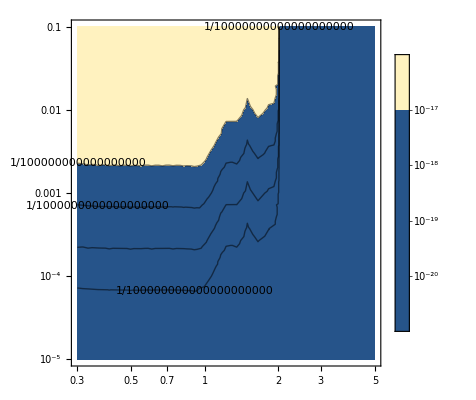

```mathematica
ContourPlot[ΓBtoXsππBRDM[mϕ,α,0]/.{qH.b2:>mϕ^2}/.formFactors/.values/.masses/.couplings/.ckms,{mϕ,0.3,5},{α,10^-5,1 10^-1},Contours-> {10^-20,10^-19,10^-18,10^-17},PlotLegends->Automatic,ContourLabels->True, PlotRange->Full,ScalingFunctions->{"Log","Log"}]
```

```mathematica
ΓBtoXsππBRDM[1,10^-4,0]
```

1.67564×10^-20+0. ⅈ

significance at BaBar

#### Search regions

```mathematica
searchRegions[BRχ_,perc_]:=ContourPlot[{cτϕBRDM[mϕ,α,BRχ]==0.5,cτϕBRDM[mϕ,α,BRχ]==100,(expDecay[RCDC,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc,(expDecay[dres,π/2,mϕ,α,BRχ]/.Belle2params)==perc,(expDecay[50,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc,(expDecay[1,π/2,mϕ,α,BRχ]/.Belle2params)==perc},{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"RegionsOfProbeability",PlotLegends->{"Efficiencies of BaBar paper, low cτ","Efficiencies of BaBar paper, high cτ",StringForm["decay to ``% inside of CDC",100*perc], StringForm["decay to ``% outside of dres",100*perc],StringForm["decay to ``% inside of 50cm",100*perc],StringForm["decay to ``% outside of 1cm",100*perc]}]
```

```mathematica
searchRegions[0.9,0.99]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

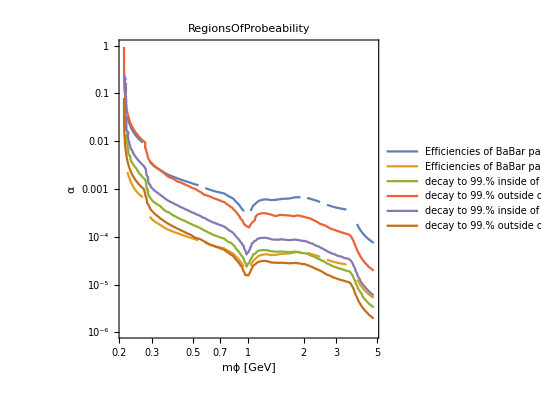

```mathematica
searchRegions[0,0.99]
```

```mathematica
probeability[BRχ_,perc_]:=Rasterize[ContourPlot[{cτϕBRDM[mϕ,α,BRχ]==0.5,cτϕBRDM[mϕ,α,BRχ]==100,(expDecay[dres,π/2,mϕ,α,BRχ]/.Belle2params)==perc,(expDecay[RCDC,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc,(expDecay[RKLM,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc},{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourLabels->{"cτ=0.5cm","cτ=100cm","d_0=100µm","d_0=162cm","d_0=300cm"},PlotRange -> Full,PlotLegends->{"cτ=0.5cm","cτ=100cm",StringForm["d_0=100µm"], StringForm["d_0=162cm"],StringForm["d_0=300cm"]},AxesStyle->Black,LabelStyle->Directive[Black,14]]]
```

InterpolatingFunction::dmval: Input value {0.200046} lies outside the range of data in the interpolating function. Extrapolation will be used.

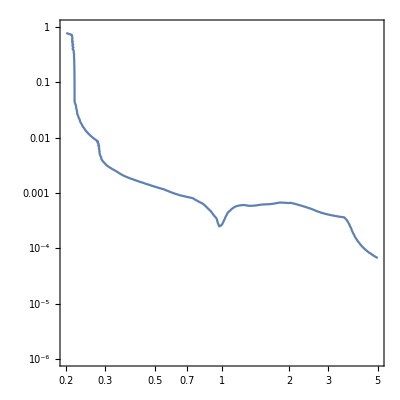

```mathematica
ContourPlot[cτϕBRDM[mϕ,α,0]==0.5,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None]
```

```mathematica
probeability[0,0.99]
Export["results/probeability.png",%]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

results/probeability.png

```mathematica
cτϕBRDM[0.28,10^-4,0]//N
```

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

(2.×10^-14)/((5.76811×10^-18+0. ⅈ)+5.20297×10^-18 HeavisideTheta[0.])

```mathematica
FindRoot[cτϕBRDM[0.28,α,0]==100,{α,4 10^-4}]
```

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {-100.+(2.×10^-14)/((9.22897×10^-17+0. ⅈ)+8.32475×10^-17 HeavisideTheta[0.])} is not a list of numbers with dimensions {1} at {α} = {0.0004}.

FindRoot[cτϕBRDM[0.28,α,0]==100,{α,4/10^4}]

```mathematica
(* re-colour, label, get rid of holes *)
```

#### pT and definitions

```mathematica
Ksvalues={mKs:>0.4976 (*GeV*),cτKs:>0.9*10^(-10) (*τ in s*)*2.998*10^10(*c in cm/s*),ϵKsB2:>0.774} (* efficiency from Florian's email, mass and cτ from PDG *);
```

```mathematica
pT[mϕ_]:=ReadList[File[ToString[StringForm["Experimental_files/BaBar_bounds/Supplemental_matherial/PT_distribution_``.txt",ToString[mϕ]]]],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}]
```

ReadList::readn: Invalid real number found when reading from Experimental_files/BaBar_bounds/Supplemental_matherial/PT_distribution_0.5.txt.

ReadList::readn: Invalid real number found when reading from Experimental_files/BaBar_bounds/Supplemental_matherial/PT_distribution_2.txt.

ReadList::readn: Invalid real number found when reading from Experimental_files/BaBar_bounds/Supplemental_matherial/PT_distribution_3.txt.

General::stop: Further output of ReadList::readn will be suppressed during this calculation.

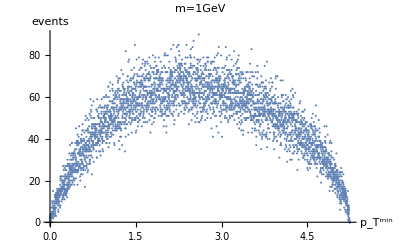
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[pT[m],AxesLabel->{"p_T^min","events"},PlotLabel->StringForm["m=``GeV",m]],{m,{0.5,1,2,3,4,5,6,7,8,9,9.5}}]
```

```mathematica
pTmax=Interpolation[{{0.5,2.5},{1,2.5},{2,2.5},{3,2.5},{4,2.5},{5,1.2},{6,0.9},{7,0.5},{8,0.2},{9,0.06},{9.5,0.02}},InterpolationOrder->1](* function in mϕ *) (* denotes approximate pTmin-point with the maximal number of events *)
```

InterpolatingFunction[…]

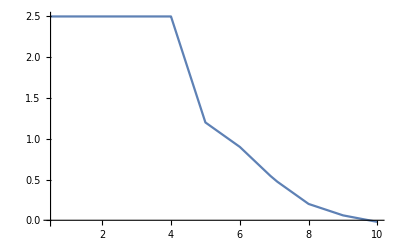

```mathematica
Plot[pTmax[m],{m,0.5,10}]
```

#### efficiency

```mathematica
effmumu=ReadList[File["Experimental_files/BaBar_bounds/Supplemental_matherial/efficiency_mumu.txt"],{Real,Real,Real, Real, Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}] (* m, cτ, pTmin, ϵ, Δϵ *) (* deleted first line in file *);
```

```mathematica
effmumuwoΔ=effmumu/.{{a_,b_,c_,d_,e_}:>{a,b,c,d}}(* m, cτ, pTmin, ϵ *);
```

```mathematica
efficiencyBaBar=Interpolation[effmumuwoΔ, InterpolationOrder->1] (* function in mϕ, cτ, pT *) (* Interpolation of values from BaBar paper *);
```

```mathematica
effBaBar[mϕ_,cτ_,pT_]:=If[mϕ≥0.5&&mϕ≤9.5&&cτ≥0.5&&cτ≤100&&pT≥0.1&&pT≤4,efficiencyBaBar[mϕ,cτ,pT],0]
```

```mathematica
(*efficiencyBelleII[mϕ_,α_,BRχ_]:=ϵKsB2/efficiencyBaBar[mKs,cτKs,pTmax[mϕ]] effBaBar[mϕ,Re[cτϕBRDM[mϕ,α,BRχ]],pTmax[mϕ]]/.Ksvalues *)(* distribution as at BaBar with value at Ks mass fixed to that at Belle II as given by the email *)
```

```mathematica
efficiencyBelleII[mϕ_,α_,BRχ_]:=effBaBar[mϕ,Re[cτϕBRDM[mϕ,α,BRχ]],pTmax[mϕ]]
```

```mathematica
efficiencyBelleII[2.2,0.0001,0]
```

InterpolatingFunction::dmval: Input value {2.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.369831

```mathematica
extrapeffBaBar[mϕ_,cτ_,pT_]:=Max[efficiencyBaBar[mϕ,cτ,pT],0]
```

```mathematica
(*extrapeffBelleII[mϕ_,α_,BRχ_]:=ϵKsB2/efficiencyBaBar[mKs,cτKs,pTmax[mϕ]] extrapeffBaBar[mϕ,Re[cτϕBRDM[mϕ,α,BRχ]],pTmax[mϕ]]/.Ksvalues*)
```

```mathematica
extrapeffBelleII[mϕ_,α_,BRχ_]:=extrapeffBaBar[mϕ,Re[cτϕBRDM[mϕ,α,BRχ]],pTmax[mϕ]]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

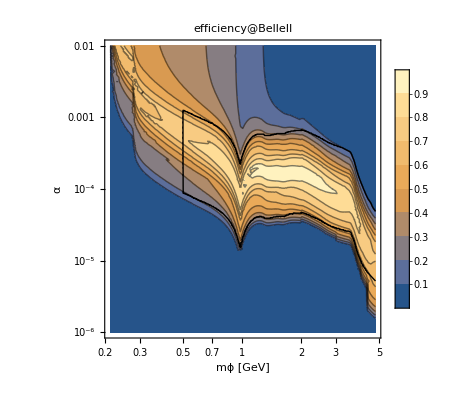

```mathematica
Show[ContourPlot[extrapeffBelleII[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-2},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"efficiency@BelleII",PlotLegends->Automatic],ContourPlot[efficiencyBelleII[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-2},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"efficiency@BelleII",PlotLegends->Automatic,Contours->{0.1},ContourShading->None,ContourStyle->Black,MaxRecursion->3]]
```

#### (n̄)_s

```mathematica
nsbar[mϕ_,α_,BRχ_]:=
NB (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]  (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
Block[{NB=NBBBelleII/.Belle2params,γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},nsbar[1,10^-4,0]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

31.5247+0. ⅈ

```mathematica
nsbarBelleII[mϕ_,α_,BRχ_]:=
NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],1,50,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ](* geometry of 1-50 cm BaBar search region, but at Belle II *) extrapeffBelleII[mϕ,α,BRχ] (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIpion[mϕ_,α_,BRχ_]:=
NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsππBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kππ *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],1,50,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ](* geometry of 1-50 cm BaBar search region, but at Belle II *) extrapeffBelleII[mϕ,α,BRχ] (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelle[mϕ_,α_,BRχ_]:=NBBBelle (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],1,50,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ](* geometry of 1-50 cm BaBar search region, but at Belle *) extrapeffBelleII[mϕ,α,BRχ] (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belleparams
```

```mathematica
ContourPlot[nsbarBelleII[m,α,NBBBelleII0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"N_S@BelleII",PlotLegends->Automatic,ColorFunction->ColorData["SolarColors"],Contours->Automatic]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ReplaceAll::reps: {Ksvalues} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 5.43×10^-322+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 1.04338×10^-318+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.60241}. NIntegrate obtained 2.388×10^-320+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 2.7369×10^-307 (8.63509×10^-10+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.75466×10^-307 (0.000163264+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.61636×10^-305 (0.0000101501+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
PlotContoursManually[nsbarBelleII,0,2mμ/.masses,mB-mK/.masses,10^-6,1,1,5*10^7,{1,10,100,1000,10000,100000,1000000,10000000}]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.60241}. NIntegrate obtained 3.2816×10^-320+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 1.14×10^-322+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 1.947×10^-321+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 7.87807×10^-308 (1.94292×10^-6+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.87584×10^-307 (0.0028948+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.88041×10^-308 (0.0000161648+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

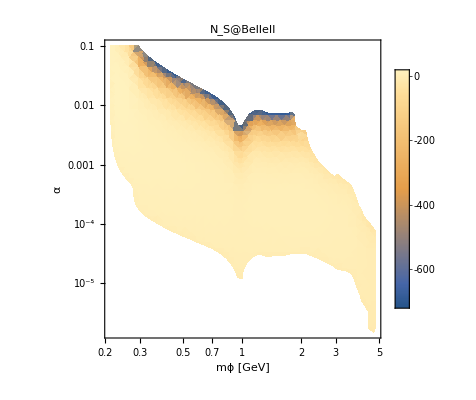

```mathematica
DensityPlot[Log[nsbarBelleII[m,α,0]]/.HeavisideTheta[0]:>1,{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"N_S@BelleII",PlotLegends->Automatic,AxesStyle->Black,FrameStyle->Black,LabelStyle->Directive[Black,14],PlotLegends->Automatic,Exclusions->None,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

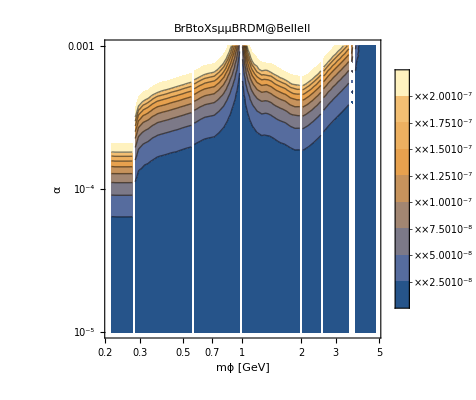

```mathematica
ContourPlot[BrBtoXsμμBRDM[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-5,10^-3},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"BrBtoXsμμBRDM@BelleII",PlotLegends->Automatic]
```

#### Belle II Searchable region

```mathematica
nsbarBelleIIfullCDC[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIfullCDCpions[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsππBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kππ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]] /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIfullCDCandKLM[mϕ_,α_,BRχ_]:=NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)GeomIntBelleII[θminBoost[θKLMMin,RKLM,cτB,γβB],θmaxBoost[θKLMMax,RKLM,cτB,γβB],dres,RKLM,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] (* geometry of 1-50 cm BaBar search region, but at Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

MuonseffmumuwoΔ=effmumu/.{{a_,b_,c_,d_,e_}:>{a,b,c,d}}(* m, cτ, pTmin, ϵ *);
efficiencyBaBar=Interpolation[effmumuwoΔ, InterpolationOrder→1] (* function in mϕ, cτ, pT *) (* Interpolation of values from BaBar paper *);
effBaBar[mϕ_,cτ_,pT_]:=If[mϕ≥0.5&&mϕ≤9.5&&cτ≥0.5&&cτ≤100&&pT≥0.1&&pT≤4,efficiencyBaBar[mϕ,cτ,pT],0]
efficiencyBelleII[mϕ_,α_,BRχ_]:=ϵKsB2/efficiencyBaBar[mKs,cτKs,pTmax[mϕ]] effBaBar[mϕ,Re[cτϕBRDM[mϕ,α,BRχ]],pTmax[mϕ]]/.Ksvalues (* distribution as at BaBar with value at Ks mass fixed to that at Belle II as given by the email *)

Muons

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

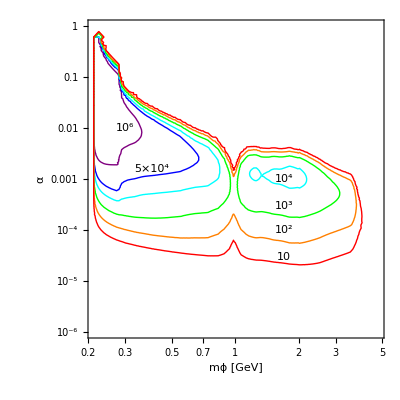

results/BelleII/NSatBelleIIFullCDC.png

```mathematica
contours={10.0,100.0,1000.0,10000.0, 50000.0,1.0 10^6};
ScientificContours={"10","10^2","10^3","10^4","5×10^4","10^6"};
pos={{1.7,3 10^-5},{1.7,1 10^-4},{1.7,3 10^-4},{1.7,1 10^-3},{0.4,1.6 10^-3},{0.3,1 10^-2}}/.{x_,y_}->{Log[x],Log[y]};
ContourPlot[nsbarBelleIIfullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},Exclusions->None,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->contours,ContourShading->None, PlotRange->{Full,Full,All},ContourStyle->{Red,Orange,Green,Cyan, Blue,Purple},Epilog->{Thread[Text[ScientificContours,pos]]}]
Export["results/BelleII/NSatBelleIIFullCDC.png",%]
```

Pions

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

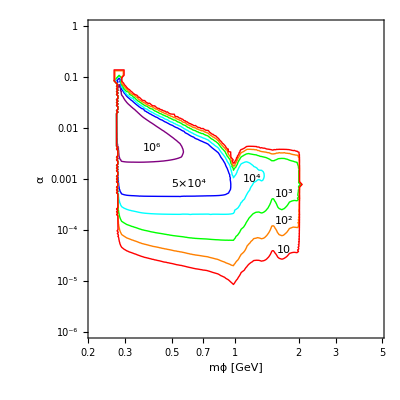

results/BelleII/NSatBelleIIFullCDCpions.png

```mathematica
contours={10.0,100.0,1000.0,10000.0, 50000.0,10^6};
ScientificContours={"10","10^2","10^3","10^4","5×10^4","10^6"};
pos={{1.7,4 10^-5},{1.7,1.5 10^-4},{1.7,5 10^-4},{1.2,1 10^-3},{0.6,8 10^-4},{0.4,4 10^-3}}/.{x_,y_}->{Log[x],Log[y]};
ContourPlot[nsbarBelleIIfullCDCpions[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},Exclusions->None,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->contours,ContourShading->None, PlotRange->{Full,Full,All},ContourStyle->{Red,Orange,Green,Cyan, Blue,Purple},Epilog->{Thread[Text[ScientificContours,pos]]}]
Export["results/BelleII/NSatBelleIIFullCDCpions.png",%]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

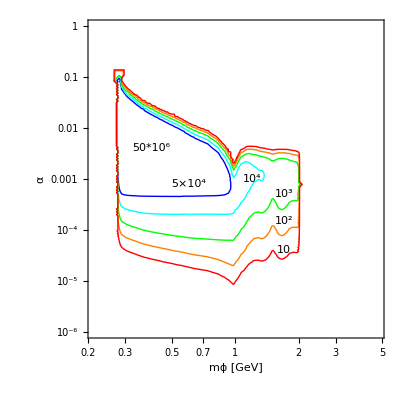

```mathematica
contours={10.0,100.0,1000.0,10000.0, 50000.0,50 10^6};
ScientificContours={"10","10^2","10^3","10^4","5×10^4","50*10^6"};
pos={{1.7,4 10^-5},{1.7,1.5 10^-4},{1.7,5 10^-4},{1.2,1 10^-3},{0.6,8 10^-4},{0.4,4 10^-3}}/.{x_,y_}->{Log[x],Log[y]};
ContourPlot[nsbarBelleIIfullCDCpions[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},Exclusions->None,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->contours,ContourShading->None, PlotRange->{Full,Full,All},ContourStyle->{Red,Orange,Green,Cyan, Blue,Purple},Epilog->{Thread[Text[ScientificContours,pos]]}]
```

```mathematica
ContourPlot[nsbarBelleIIfullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"N_S@BelleII-CDC",ContourStyle->ColorFunction["Rainbow"],Contours->{10,100,1000,10000, 20000,30000},ContourShading->None,ContourLabels->True,Epilog->{Thread[Text[contours,pos]]}]
```

```mathematica
ContourPlot[nsbarBelleIIfullCDC[m,α,0]==10,{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"N_S@BelleII-CDC",ContourStyle->Red,ContourLabels->Text,ContourShading->None]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Throw::nocatch: Uncaught Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation] returned to top level.

General::stop: Further output of Throw::nocatch will be suppressed during this calculation.

Hold[Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation],Throw[Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y''[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation]]

```mathematica
BIIsr[BRχ_,nS_]:=Show[ContourPlot[nsbarBelleIIfullCDC[m,α,BRχ],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{nS}],ContourPlot[nsbarBelleIIfullCDCandKLM[m,α,BRχ],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Directive[Dashed,Black]},Contours->{nS}]]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

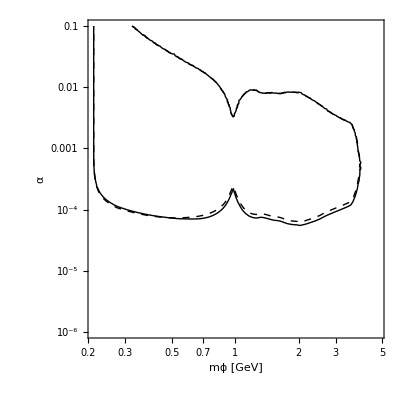

```mathematica
BIIsr[0,100]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

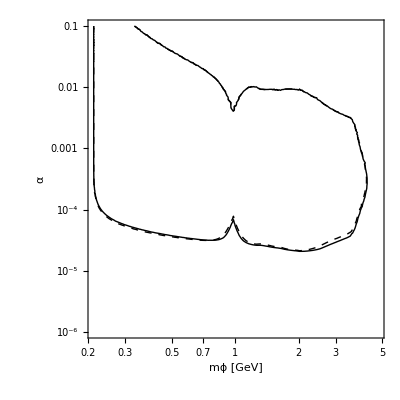

```mathematica
BIIsr[0,10]
```

```mathematica
(* Why KLM not better than CDC and why even worse? *)
```

#### Belle Searchable region

```mathematica
nsbarBellefullCDC[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelle (* number of BB pairs at Belle *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)GeomIntBelleCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]] /.formFactors/.values/.masses/.couplings/.ckms/.Belleparams
```

```mathematica
nsbarBellefullCDCpions[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelle (* number of BB pairs at Belle*)BrBtoXsππBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kππ *)GeomIntBelleCDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]] /.formFactors/.values/.masses/.couplings/.ckms/.Belleparams
```

Muons

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::nlim: θ = ArcTan[RCDC/(-0.04914 γβB+RCDC Cot[θCDCMin])] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

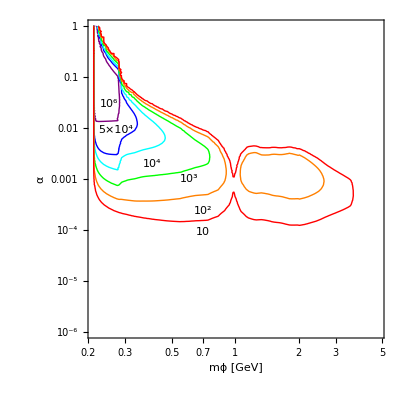

results/Belle/NSatBelleFullCDC.png

```mathematica
contours={10.0,100.0,1000.0,10000.0, 50000.0,1.0 10^6};
ScientificContours={"10","10^2","10^3","10^4","5×10^4","10^6"};
pos={{0.7,9 10^-5},{0.7,2.4 10^-4},{0.6,1 10^-3},{0.4,2 10^-3},{0.27,9 10^-3},{0.25,3 10^-2}}/.{x_,y_}->{Log[x],Log[y]};
ContourPlot[nsbarBellefullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},Exclusions->None,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->contours,ContourShading->None, PlotRange->{Full,Full,All},ContourStyle->{Red,Orange,Green,Cyan, Blue,Purple},Epilog->{Thread[Text[ScientificContours,pos]]}]
Export["results/Belle/NSatBelleFullCDC.png",%]
```

Pions

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::nlim: θ = ArcTan[RCDC/(-0.04914 γβB+RCDC Cot[θCDCMin])] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

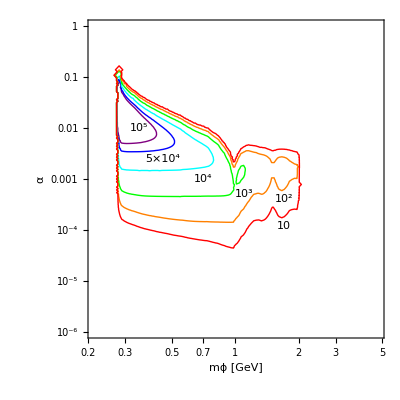

results/Belle/NSatBelleFullCDCpions.png

```mathematica
contours={10.0,100.0,1000.0,10000.0, 50000.0, 10^5};
ScientificContours={"10","10^2","10^3","10^4","5×10^4","10^5"};
pos={{1.7,1.2 10^-4},{1.7,4 10^-4},{1.1,5 10^-4},{0.7,1 10^-3},{0.45,2.5 10^-3},{0.35,10^-2}}/.{x_,y_}->{Log[x],Log[y]};
ContourPlot[nsbarBellefullCDCpions[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},Exclusions->None,ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},Contours->contours,ContourShading->None, PlotRange->{Full,Full,All},ContourStyle->{Red,Orange,Green,Cyan, Blue,Purple},Epilog->{Thread[Text[ScientificContours,pos]]}]
Export["results/Belle/NSatBelleFullCDCpions.png",%]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::nlim: θ = ArcTan[RCDC/(-0.04914 γβB+RCDC Cot[θCDCMin])] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

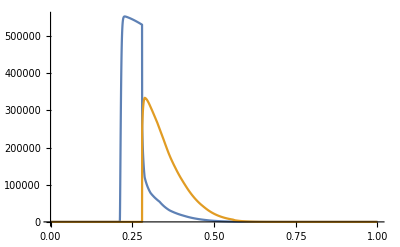

```mathematica
Plot[{nsbarBellefullCDC[mϕ,0.01,0],nsbarBellefullCDCpions[mϕ,0.01,0]},{mϕ,0,1},PlotRange->Full]
```

#### (n̄)_b

```mathematica
datapointsBGLEraw={{0.21372099,42.001694},{0.22525336,34.66641},{0.23534627,47.633167},{0.24590227,116.10976},{0.25468045,170.05653},{0.26377332,265.44833},{0.27438214,282.7244},{0.28542048,342.03513},{0.29560357,388.28183},{0.3061485,413.5817},{0.3156805,387.8666},{0.32126254,413.25732},{0.33272275,440.1846},{0.34308723,499.73773},{0.35688427,499.41702},{0.36639637,644.0592}};
```

```mathematica
datapointsBGLE=datapointsBGLEraw/.{x_,y_}-> {x,y*0.01};
```

```mathematica
datapointsBGHEraw={{0.5506243,246.10129},{0.65035075,216.07903},{0.7514895,167.08679},{0.8532689,121.26443},{0.95199466,77.50407},{1.0528985,63.918392},{1.154277,26.164131},{1.2490236,40.811565},{1.3514479,24.486633},{1.4431583,12.138965},{1.547957,13.772417},{1.6602925,8.808055},{1.8524659,9.370606},{1.9437282,2.6193016},{2.0486617,2.97261},{2.159144,1.6742009},{2.2558663,2.025275},{2.4515235,0.9417825},{3.1468844,0.93796134},{4.3517766,0.87544847},{6.6269326,0.9266568},{9.616752,0.92105573}};
```

```mathematica
datapointsBGHE={{0.5506243,246.10129},{0.65035075,216.07903},{0.7514895,167.08679},{0.8532689,121.26443},{0.95199466,77.50407},{1.0528985,63.918392},{1.154277,26.164131},{1.2490236,40.811565},{1.3514479,24.486633},{1.4431583,12.138965},{1.547957,13.772417},{1.6602925,8.808055},{1.8524659,9.370606},{1.9437282,2.6193016},{2.0486617,2.97261},{2.159144,1.6742009},{2.2558663,2.025275},{2.4515235,0.9417825/2 (* 2 100MeV steps to the last value *)},{3.1468844,0.93796134/7},{4.3517766,0.87544847/12},{6.6269326,0.9266568/23},{9.616752,0.92105573/30}}/.{x_,y_}-> {x,y*0.1};
```

```mathematica
nbbarBaBar[mϕ_]:=If[mϕ<0.37&&mϕ>2mμ/.masses,Interpolation[datapointsBGLE,mϕ,InterpolationOrder->1],If[mϕ>0.5&&mϕ<mB-mK/.masses,Interpolation[datapointsBGHE,mϕ,InterpolationOrder->1],Indeterminate]]
```

```mathematica
nbbarBelleII[mϕ_]:=NBBBelleII/NBBBaBar nbbarBaBar[mϕ]/.Belle2params/.{NBBBaBar->4.484*10^8}
```

```mathematica
nbbarBelle[mϕ_]:=NBBBelle/NBBBaBar nbbarBaBar[mϕ]/.Belleparams/.{NBBBaBar->4.484*10^8}
```

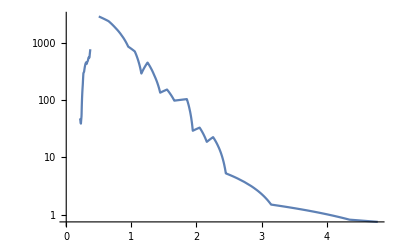

```mathematica
LogPlot[nbbarBelleII[m],{m,0,mB-mK/.masses}]
```

```mathematica
datapointsBGππ={{0.9131339,2221.6843},{1.0125622,1390.329},{1.113701,1076.215},{1.2116822,798.4914},{1.3111305,592.47107},{1.4110401,421.33566},{1.5103257,312.663},{1.6165973,232.01965},{1.7116226,179.67429},{1.817167,133.34377},{1.9135458,107.750946},{2.0150402,90.85127},{2.1161292,59.358723},{2.2102349,40.46926},{2.3148234,30.038363},{2.4112244,26.430117},{2.5116065,17.26995},{2.6161926,13.956961},{2.717725,10.810403},{2.8155599,10.806249},{2.916867,7.368078},{3.013638,6.213753},{3.1136138,5.02218},{3.2169063,4.0591073},{3.314621,3.8889086},{3.4152262,2.2371058},{3.518965,2.1433039},{3.6160042,2.053496},{3.7157054,1.8070945},{3.8181627,1.6593171},{3.9127345,1.1315142},{4.009861,2.5369604},{4.210921,0.9538217/2},{4.315376,1.4587036},{4.410365,1.8037322},{4.519451,0.57226205},{4.720497,0.52537143/2},{4.811243,0.5034021},{5.1079974,0.52492124/3},{5.220385,0.52479714},{5.3207507,0.52468854},{5.423025,0.48182422},{6.332658,0.48101303/9},{6.7599325,0.5015454/4},{7.5165772,0.5009675/8},{8.111523,0.52228993/6},{8.200506,0.98806006},{8.312547,0.4795932},{8.5186,0.50028676/2},{8.825276,0.5218115/3},{9.217865,0.47905475/4},{9.319002,0.9456238},{9.627973,0.4996217/3},{9.840052,0.86803764/2},{9.866578,0.45877808}};
```

```mathematica
nbbarBaBarππ[mϕ_]:=If[mϕ>0.86,Interpolation[datapointsBGππ,mϕ,InterpolationOrder->1],Indeterminate]
```

```mathematica
nbbarBelleIIππ[mϕ_]:=NBBBelleII/NBBBaBar nbbarBaBarππ[mϕ]/.Belle2params/.{NBBBaBar->4.484*10^8}
```

InterpolatingFunction::dmval: Input value {0.87903} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

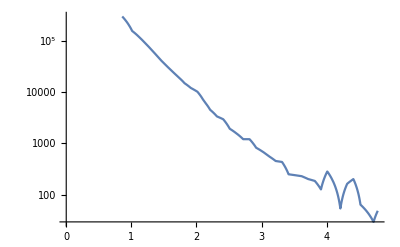

```mathematica
LogPlot[nbbarBelleIIππ[m],{m,0,mB-mK/.masses}]
```

#### Significance

```mathematica
significance[mϕ_,α_,BRχ_]:=nsbarBelleII[mϕ,α,BRχ]/Sqrt[nsbarBelleII[mϕ,α,BRχ]+nbbarBelleII[mϕ]]
```

```mathematica
significanceππ[mϕ_,α_,BRχ_]:=nsbarBelleIIpion[mϕ,α,BRχ]/Sqrt[nsbarBelleIIpion[mϕ,α,BRχ]+nbbarBelleIIππ[mϕ]]
```

```mathematica
significanceBelle[mϕ_,α_,BRχ_]:=nsbarBelle[mϕ,α,BRχ]/Sqrt[nsbarBelle[mϕ,α,BRχ]+nbbarBelle[mϕ]]
```

```mathematica
ContourPlot[significance[mϕ,α,0]==1.96,{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14]]
```

NIntegrate::inumr: The integrand 1/2 (-ⅇ^(-3.81915×10^15 ⅇ^(«30») «1» (9.15868×10^-14 Power[«2»] Plus[«5»] Power[«2»]+5.1673×10^-7 Power[«2»] Power[«2»] Plus[«3»] HeavisideTheta[«1»] Power[«2»]+«10»+(Power[«2»] Power[«2»] Power[«2»] HeavisideTheta[«1»] Power[«2»] Power[«2»])/1936512))+ⅇ^(-7.6383×10^13 ⅇ^(Charting`Private`pvar$11748187) Csc[θ] («1»))) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296712,2.61801}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
RegionPlot[significance[Exp[Logmϕ],Exp[Logα],0]>=1.96,{Logmϕ,Log[2mμ/.masses],Log[mB-mK/.masses]},{Logα,Log[10^-6],Log[1]},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14]]
```

NIntegrate::inumr: The integrand 1/2 (-ⅇ^(-3.81915×10^15 ⅇ^(«5») «1» (9.15868×10^-14 Power[«2»] Plus[«5»] Power[«2»]+5.1673×10^-7 Power[«2»] Power[«2»] Plus[«3»] HeavisideTheta[«1»] Power[«2»]+«10»+(Power[«2»] Power[«2»] Power[«2»] HeavisideTheta[«1»] Power[«2»] Power[«2»])/1936512))+ⅇ^(«1»)) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296712,2.61801}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212035} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Throw::nocatch: Uncaught Throw[-Holonomic`DifferentialRootReduceDump`y[NIntegrate`LevinRuleDump`x]+Holonomic`DifferentialRootReduceDump`y'[NIntegrate`LevinRuleDump`x],NIntegrate`LevinRuleDump`FastLookupHolonomicDifferentialEquation] returned to top level.

General::stop: Further output of Throw::nocatch will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 2.0041×10^-319+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 3.47373×10^-319+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

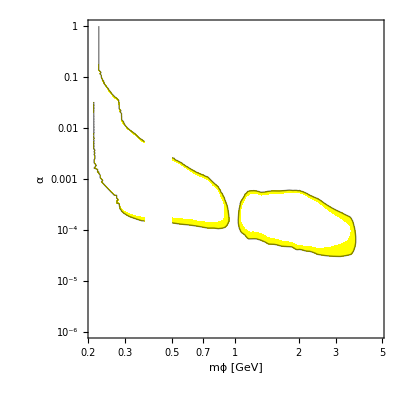

```mathematica
ContourPlot[significance[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},PlotRange-> Full,ContourShading->{White,Yellow}]
```

Belle II, muons. 3 events + sensitivity

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 2.0041×10^-319+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 3.47373×10^-319+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

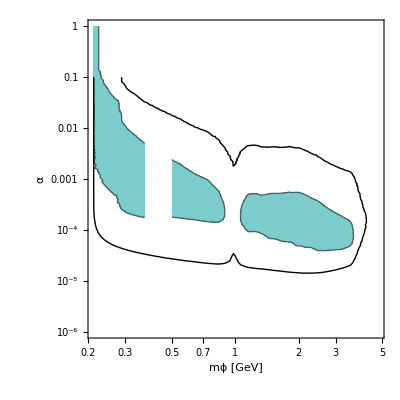

```mathematica
Belle2Comp=Show[ContourPlot[significance[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,RGBColor[0.49,0.80,0.8]},PlotRange->Full],ContourPlot[nsbarBelleIIfullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}]]
```

```mathematica
Export["results/BelleII/NSatBelleII-BaBareff+3events.png",Belle2Comp]
```

results/BelleII/NSatBelleII-BaBareff+3events.png

sensitivity muons-pions at Belle II

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: (1.34031×10^-307+0. ⅈ) (0.00184652+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.59577×10^-308+0. ⅈ) (0.00183777+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.75384×10^-308+0. ⅈ) (0.00183561+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

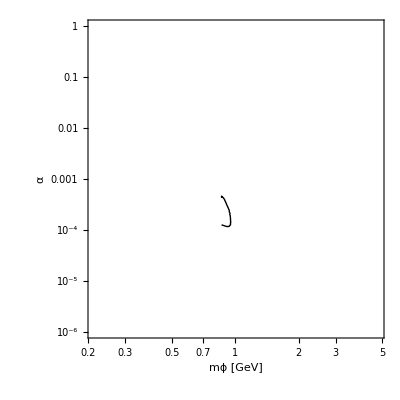

```mathematica
ContourPlot[significanceππ[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,Dashed,14],Exclusions->None,Contours->{1.96},ContourShading->None,PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 2.0041×10^-319+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 3.47373×10^-319+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: (1.34031×10^-307+0. ⅈ) (0.00184652+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.59577×10^-308+0. ⅈ) (0.00183777+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.75384×10^-308+0. ⅈ) (0.00183561+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

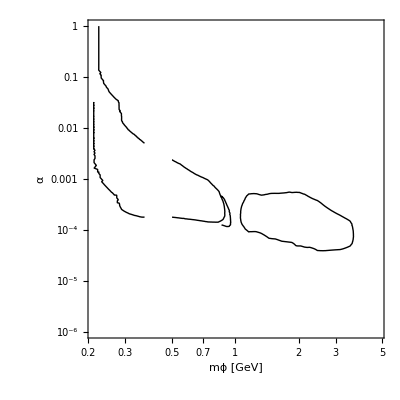

results/BelleII/sensitivity_BelleII_muons-pions.png

```mathematica
Show[ContourPlot[significance[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->None,PlotRange->Full],ContourPlot[significanceππ[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,Dashed,14],Exclusions->None,Contours->{1.96},ContourShading->None,PlotRange->Full]]
Export["results/BelleII/sensitivity_BelleII_muons-pions.png",%]
```

Belle II, 3 events for muons and pions

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

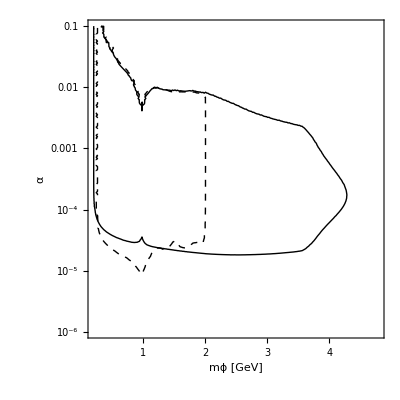

results/BelleII/BelleII_3events_muons-pions_newboost_nonlog.png

```mathematica
Show[ContourPlot[nsbarBelleIIfullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],
ContourPlot[nsbarBelleIIfullCDCpions[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}]]
Export["results/BelleII/BelleII_3events_muons-pions_newboost_nonlog.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

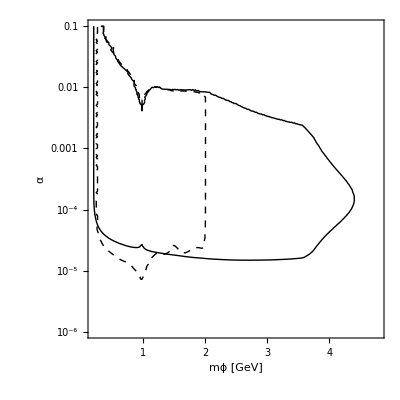

results/BelleII/BelleII_3events_muons-pions_newboost_nonlog_twiceNB_XS.png

```mathematica
Show[ContourPlot[2 nsbarBelleIIfullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],
ContourPlot[2nsbarBelleIIfullCDCpions[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}]]
Export["results/BelleII/BelleII_3events_muons-pions_newboost_nonlog_twiceNB_XS.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

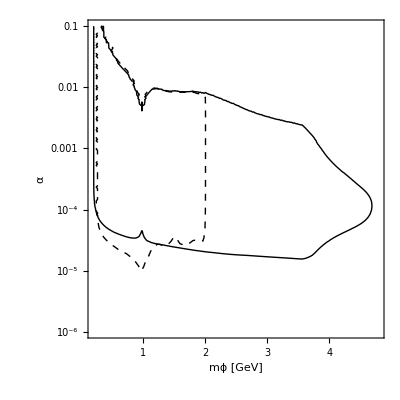

```mathematica
Show[ContourPlot[8 nsbarBelleIIfullCDCK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],
ContourPlot[8 nsbarBelleIIfullCDCpionsK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}]]
(*Export["results/BelleII/BelleII_3events_muons-pions_newboost_twiceNB_nonlog.png",%]*)
```

Belle

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

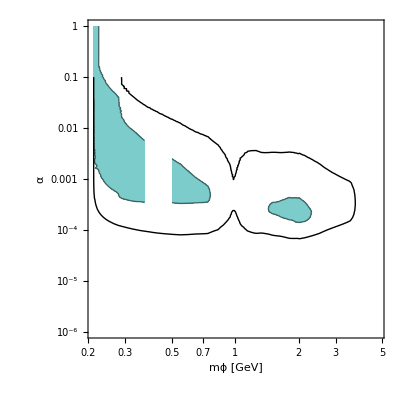

results/Belle/NSatBelle-BaBareff+3events.png

```mathematica
BelleComp=Show[ContourPlot[significanceBelle[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,RGBColor[0.49,0.80,0.8]},PlotRange->Full],ContourPlot[nsbarBellefullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}]]
Export["results/Belle/NSatBelle-BaBareff+3events.png",BelleComp]
```

Belle, 3 events for muons and pions

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

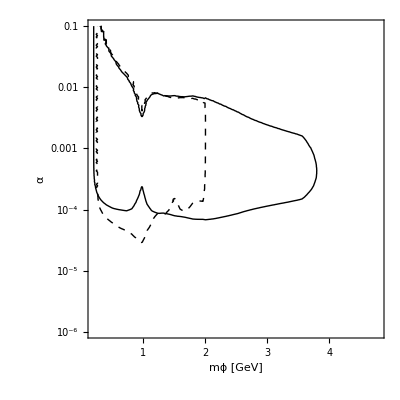

results/Belle/Belle_3events_muons-pions_nonlog_newboost.png

```mathematica
Show[ContourPlot[nsbarBellefullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],
ContourPlot[nsbarBellefullCDCpions[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}]]
Export["results/Belle/Belle_3events_muons-pions_nonlog_newboost.png",%]
```

3 events for muons, Belle parameters, different boosts

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

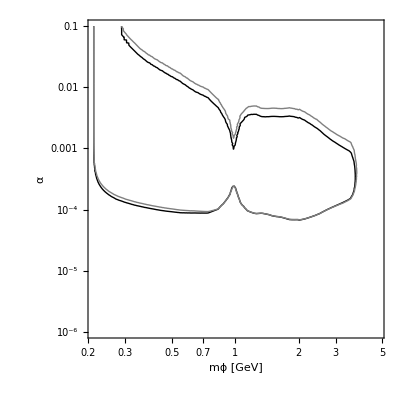

results/Belle-Belle2_3events_boosts.png

```mathematica
Show[ContourPlot[Block[{NB=NBBBelle/.Belleparams,γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},nsbar[m,α,0]],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],ContourPlot[Block[{NB=NBBBelle/.Belleparams,γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},nsbar[m,α,0]],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Gray},Contours->{3}]]
Export["results/Belle-Belle2_3events_boosts.png",%]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

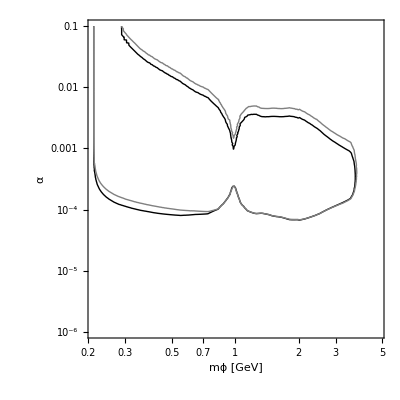

results/Belle-Belle2_3events_boosts+RCDC.png

```mathematica
Show[ContourPlot[Block[{NB=NBBBelle/.Belleparams,γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belle2params,dres=dres/.Belleparams},nsbar[m,α,0]],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],ContourPlot[Block[{NB=NBBBelle/.Belleparams,γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},nsbar[m,α,0]],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Gray},Contours->{3}]]
Export["results/Belle-Belle2_3events_boosts+RCDC.png",%]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

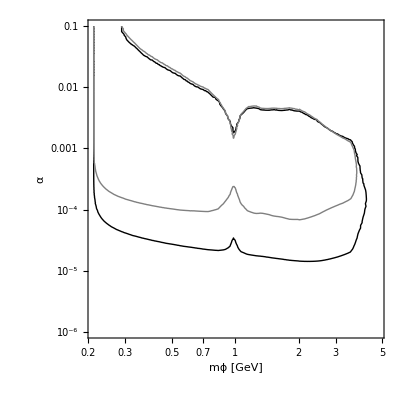

results/Belle-Belle2_3events_boosts+RCDC+Lumi.png

```mathematica
Show[ContourPlot[Block[{NB=NBBBelleII/.Belle2params,γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belle2params,dres=dres/.Belleparams},nsbar[m,α,0]],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],ContourPlot[Block[{NB=NBBBelle/.Belleparams,γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},nsbar[m,α,0]],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Gray},Contours->{3}]]
Export["results/Belle-Belle2_3events_boosts+RCDC+Lumi.png",%]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 1.358×10^-305 (1.36826×10^-9+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

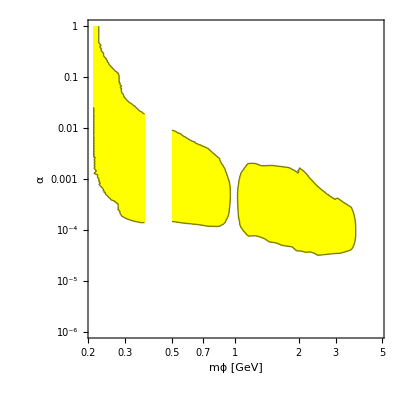

```mathematica
ContourPlot[significance[mϕ,α,0.5],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,Yellow},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 0.15629 (5.78059×10^-308+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 1.3236×10^-320+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 7.×10^-323+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 8.16506×10^-305 (0.0000107405+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

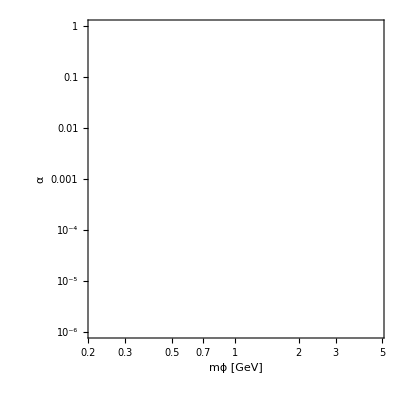

```mathematica
Show[ContourPlot[significance[mϕ,α,0.5],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,Yellow},PlotRange->Full],
ContourPlot[significance[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,Cyan},PlotRange->Full]]
```

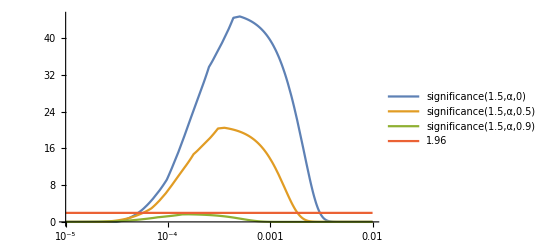

```mathematica
LogLinearPlot[{significance[1.5,α,0],significance[1.5,α,0.5],significance[1.5,α,0.9],1.96},{α,10^-5,10^-2},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
significance[1.5,0.003,0]
```

InterpolatingFunction::femdmval: Input value {1.5,0.021136,2.5} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.4976,2.6982,2.5} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {1.5,0.021136,2.5} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

1.25906×10^-45+0. ⅈ

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 1.6602×10^-304 (5.40042×10^-10+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

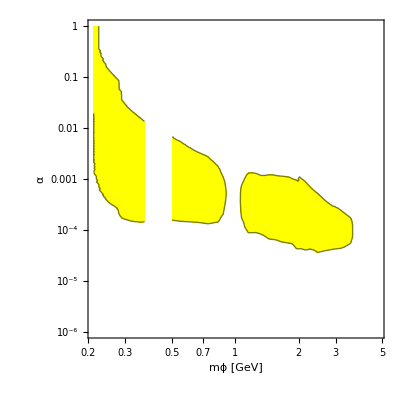

```mathematica
ContourPlot[significance[mϕ,α,0.7],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,Yellow},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 9.42006×10^-299 (1.01223×10^-10+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

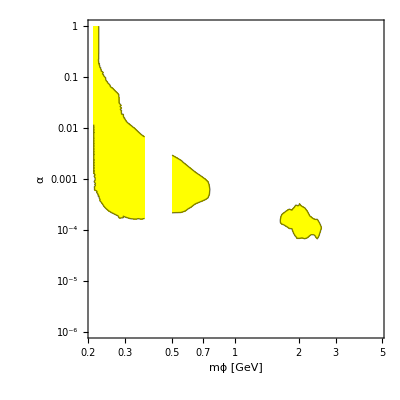

```mathematica
ContourPlot[significance[mϕ,α,0.9],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,Yellow},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 4.975×10^-321+0. ⅈ and 0. for the integral and error estimates.

General::munfl: 1.47828×10^-307 (0.0000165957+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 1.06×10^-320+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 2.72417×10^-307 (0.000016565+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

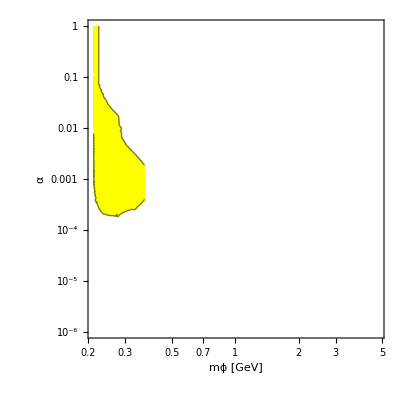

```mathematica
ContourPlot[significance[mϕ,α,0.98],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,Yellow},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45733}. NIntegrate obtained 2.0041×10^-319+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 3.47373×10^-319+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

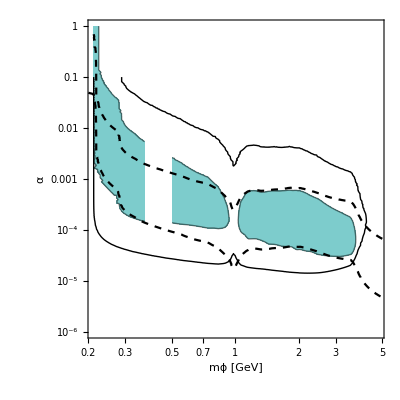

```mathematica
Belle2CompLifetime=Show[ContourPlot[significance[mϕ,α,0],{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},AxesStyle->Black,LabelStyle->Directive[Black,14],Exclusions->None,Contours->{1.96},ContourShading->{White,RGBColor[0.49,0.80,0.8]},PlotRange->Full],
ContourPlot[nsbarBelleIIfullCDC[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],
ContourPlot[cτϕBRDM[mϕ,α,0]==0.5,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None,ContourStyle->{Directive[Dashed,Black]}],
ContourPlot[cτϕBRDM[mϕ,α,0]==100,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None,ContourStyle->{Directive[Dashed,Black]}]]
```

```mathematica
Export["results/BelleII/NSatBelleII-BaBar+3events_lifetimes.png",Belle2CompLifetime]
```

results/BelleII/NSatBelleII-BaBar+3events_lifetimes.png

InterpolatingFunction::dmval: Input value {0.200046} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

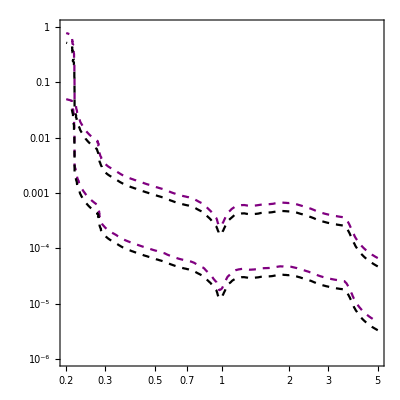

```mathematica
Show[ContourPlot[cτϕBRDM[mϕ,α,0]==0.5,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None,ContourStyle->{Directive[Dashed,Purple]}],ContourPlot[cτϕBRDM[mϕ,α,0]==100,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None,ContourStyle->{Directive[Dashed,Purple]}],
ContourPlot[cτϕBRDM[mϕ,α,0.5]==0.5,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None,ContourStyle->{Directive[Dashed,Black]}],
ContourPlot[cτϕBRDM[mϕ,α,0.5]==100,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None,ContourStyle->{Directive[Dashed,Black]}]]
```

#### Exclusive 3-event line: μ+τ & π

K^+

```mathematica
nsbarBelleIIfullCDCmuonK[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)(BrBtoKPμμBRDM[mϕ,α,0]+BrBtoKstarSμμBRDM[mϕ,α,0]+BrBtoKstarVμμBRDM[mϕ,α,0]+BrBtoKAVμμBRDM[mϕ,α,0])(* Branching ratio of B pair into Kμμ+Kττ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIfullCDCtauK[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)(BrBtoKPττBRDM[mϕ,α,0]+BrBtoKstarSττBRDM[mϕ,α,0]+BrBtoKstarVττBRDM[mϕ,α,0]+BrBtoKAVττBRDM[mϕ,α,0])(* Branching ratio of B pair into Kμμ+Kττ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIfullCDCpionK[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)(BrBtoKPππBRDM[mϕ,α,0]+BrBtoKstarSππBRDM[mϕ,α,0]+BrBtoKstarVππBRDM[mϕ,α,0]+BrBtoKAVππBRDM[mϕ,α,0])(* Branching ratio of B pair into Kππ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]] /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIfullCDCkaonK[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)(BrBtoKPKKBRDM[mϕ,α,0]+BrBtoKstarSKKBRDM[mϕ,α,0]+BrBtoKstarVKKBRDM[mϕ,α,0]+BrBtoKAVKKBRDM[mϕ,α,0])(* Branching ratio of B pair into Kππ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]] /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIfullCDCallK[mϕ_,α_,BRχ_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)(ΓBtoKPϕ[mϕ,α]+ΓBtoKstarSϕ[mϕ,α]+ΓBtoKstarVϕ[mϕ,α]+ΓBtoKstarAVϕ[mϕ,α])/ΓtotalB(* Branching ratio of B pair into Kϕ *)GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]] /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

InterpolatingFunction::dmval: Input value {1.00002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

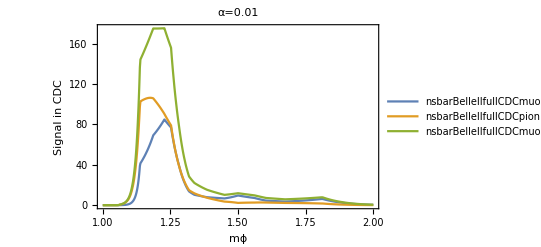

```mathematica
Show[Plot[{nsbarBelleIIfullCDCmuonK[mϕ,0.01,0],nsbarBelleIIfullCDCpionK[mϕ,0.01,0],nsbarBelleIIfullCDCmuonK[mϕ,0.01,0]+nsbarBelleIIfullCDCpionK[mϕ,0.01,0]},{mϕ,1,2},Frame->True,FrameLabel->{"mϕ","Signal in CDC"},PlotLabel->"α=0.01",PlotLegends->"Expressions",PlotRange->Full]]
```

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.963175}. NIntegrate obtained 6.1199+0. ⅈ and 1.74413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.963175}. NIntegrate obtained 6.1199+0. ⅈ and 1.74413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.963175}. NIntegrate obtained 6.1199+0. ⅈ and 1.74413 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

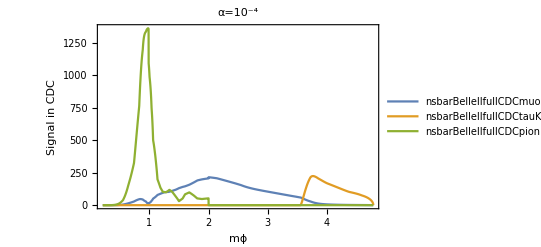

```mathematica
Show[Plot[{nsbarBelleIIfullCDCmuonK[mϕ,10^-4,0],nsbarBelleIIfullCDCtauK[mϕ,10^-4,0],nsbarBelleIIfullCDCpionK[mϕ,10^-4,0]},{mϕ,2mμ/.masses,mB-mK/.masses},Frame->True,FrameLabel->{"mϕ","Signal in CDC"},PlotLabel->"α=10^-4",PlotLegends->"Expressions",PlotRange->Full]]
```

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.23719}. NIntegrate obtained -1062.14+0. ⅈ and 175.896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.23719}. NIntegrate obtained -1062.14+0. ⅈ and 175.896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.23719}. NIntegrate obtained -1062.14+0. ⅈ and 175.896 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

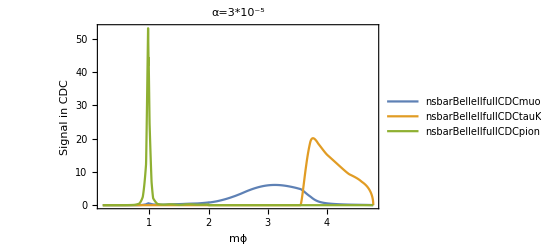

```mathematica
Show[Plot[{nsbarBelleIIfullCDCmuonK[mϕ,3 10^-5,0],nsbarBelleIIfullCDCtauK[mϕ,3 10^-5,0],nsbarBelleIIfullCDCpionK[mϕ,3 10^-5,0]},{mϕ,2mμ/.masses,mB-mK/.masses},Frame->True,FrameLabel->{"mϕ","Signal in CDC"},PlotLabel->"α=3*10^-5",PlotLegends->"Expressions",PlotRange->Full]]
```

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.62965}. NIntegrate obtained 6400.15+0. ⅈ and 812.167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.62965}. NIntegrate obtained 6400.15+0. ⅈ and 812.167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.62965}. NIntegrate obtained 6400.15+0. ⅈ and 812.167 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

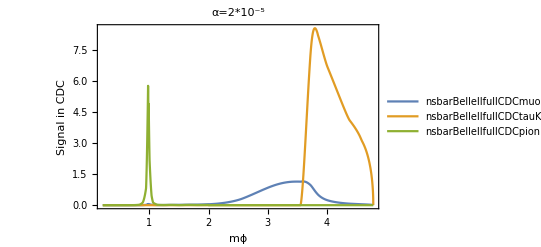

```mathematica
Show[Plot[{nsbarBelleIIfullCDCmuonK[mϕ,2 10^-5,0],nsbarBelleIIfullCDCtauK[mϕ,2 10^-5,0],nsbarBelleIIfullCDCpionK[mϕ,2 10^-5,0]},{mϕ,2mμ/.masses,mB-mK/.masses},Frame->True,FrameLabel->{"mϕ","Signal in CDC"},PlotLabel->"α=2*10^-5",PlotLegends->"Expressions",PlotRange->Full]]
```

InterpolatingFunction::dmval: Input value {0.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

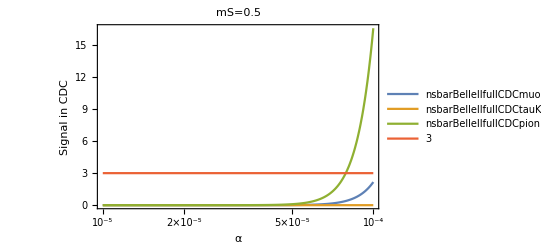

```mathematica
Show[LogLinearPlot[{nsbarBelleIIfullCDCmuonK[0.5,α,0],nsbarBelleIIfullCDCtauK[0.5,α,0],nsbarBelleIIfullCDCpionK[0.5,α,0],3},{α,10^-5,10^-4},Frame->True,FrameLabel->{"α","Signal in CDC"},PlotLabel->"mS=0.5",PlotLegends->"Expressions",PlotRange->Full]]
```

Belle II, 3 events for muons+taus and pions. Decays to K+&K*

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

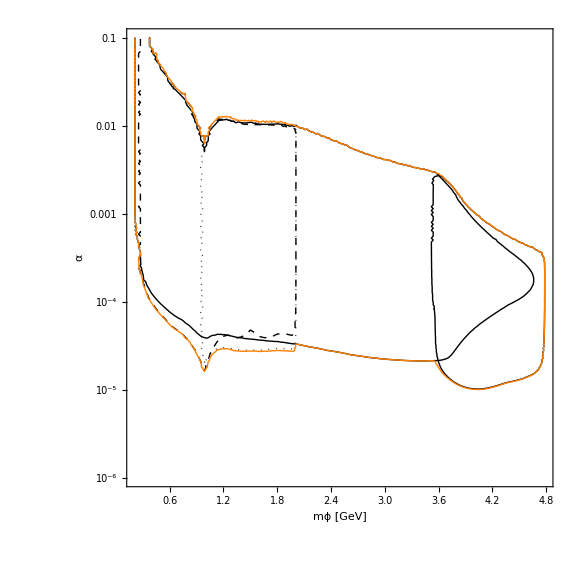

results/BelleII/BelleII_3events_muons-taus-pions-kaons_newboost_newGeomInt_S-PS-V-AV.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCmuonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black,Thick},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}],ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dotted},Contours->{3},PlotRange->Full],
ContourPlot[1.93 (nsbarBelleIIfullCDCkaonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]+nsbarBelleIIfullCDCmuonK[m,α,0]+nsbarBelleIIfullCDCtauK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Orange},Contours->{3},PlotRange->Full],ImageSize-> Large]
Export["results/BelleII/BelleII_3events_muons-taus-pions-kaons_newboost_newGeomInt_S-PS-V-AV.png",%]
```

```mathematica
Block[{m=1.2},FindRoot[1.93 (nsbarBelleIIfullCDCkaonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]+nsbarBelleIIfullCDCmuonK[m,α,0]+nsbarBelleIIfullCDCtauK[m,α,0])==3,{α,0.01}]]
```

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-1.1674×10^12 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (1/400+(8.56605×10^-14 Sin[θ] (1/20+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-3.78237×10^15 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (26244+(8.56605×10^-14 Sin[θ] (162+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.0125091+0. ⅈ}

```mathematica
Block[{m=1.2},FindRoot[nsbarBelleIIfullCDCpionK[m,α,0]==3,{α,0.01}]]
```

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-1.1674×10^12 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (1/400+(8.56605×10^-14 Sin[θ] (1/20+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-3.78237×10^15 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (26244+(8.56605×10^-14 Sin[θ] (162+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.011475+0. ⅈ}

```mathematica
Block[{m=1.2},FindRoot[nsbarBelleIIfullCDCkaonK[m,α,0]==3,{α,0.01}]]
```

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-1.1674×10^12 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (1/400+(8.56605×10^-14 Sin[θ] (1/20+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-3.78237×10^15 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (26244+(8.56605×10^-14 Sin[θ] (162+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.0122052+0. ⅈ}

```mathematica
Block[{m=1.2},FindRoot[nsbarBelleIIfullCDCallK[m,α,0]==3,{α,0.01}]]
```

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-1.1674×10^12 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (1/400+(8.56605×10^-14 Sin[θ] (1/20+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-3.78237×10^15 Csc[θ] ((0.+0. ⅈ)+(1.12895×10^-7+0. ⅈ) Power[«2»])) (26244+(8.56605×10^-14 Sin[θ] (162+4.28303×10^-14 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.0123083+0. ⅈ}

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

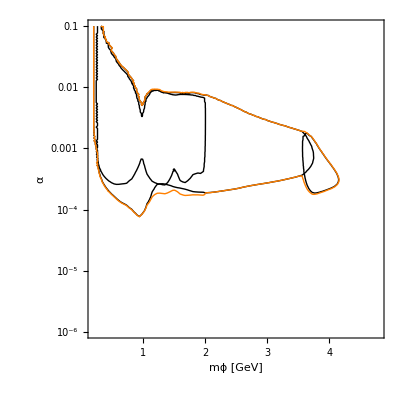

results/BelleII/BelleII_3events_muons_newboost_newGeomInt_S-PS-V-AV_100fb.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCmuonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 (nsbarBelleIIfullCDCmuonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]+nsbarBelleIIfullCDCtauK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Orange},Contours->{3},PlotRange->Full,ImageSize->Full]
]
Export["results/BelleII/BelleII_3events_muons_newboost_newGeomInt_S-PS-V-AV_100fb.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

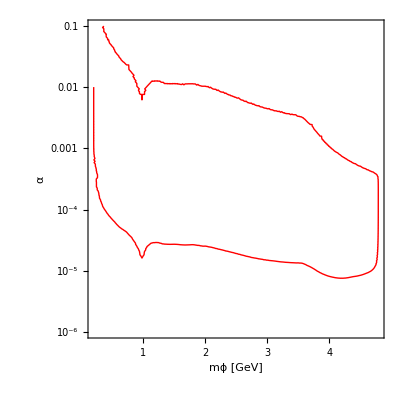

```mathematica
ContourPlot[1.93 nsbarBelleIIfullCDCallK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Red},Contours->{3},PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

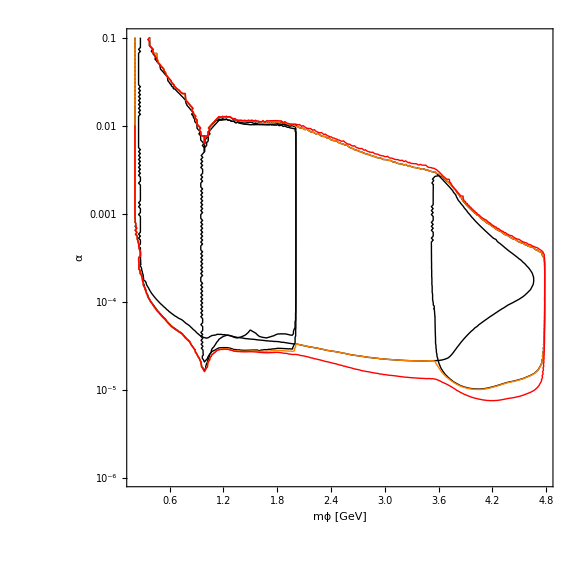

results/BelleII/BelleII_3events_muons_newboost_newGeomInt_S-PS-V-AV.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCmuonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full],ContourPlot[1.93 (nsbarBelleIIfullCDCmuonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]+nsbarBelleIIfullCDCkaonK[m,α,0]+nsbarBelleIIfullCDCtauK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Orange},Contours->{3},PlotRange->Full],
ContourPlot[1.93 nsbarBelleIIfullCDCallK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Red},Contours->{3},PlotRange->Full],ImageSize-> Large
]
Export["results/BelleII/BelleII_3events_muons_newboost_newGeomInt_S-PS-V-AV.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

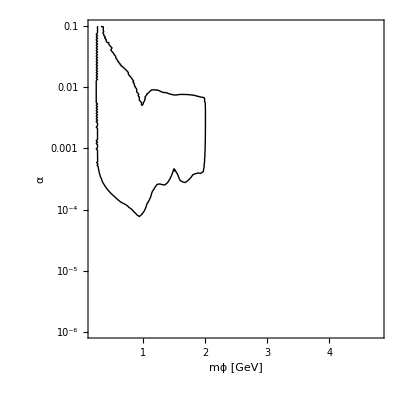

results/BelleII/BelleII_3events_pions_newboost_newGeomInt_S-PS-V-AV_100fb.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full]]
Export["results/BelleII/BelleII_3events_pions_newboost_newGeomInt_S-PS-V-AV_100fb.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

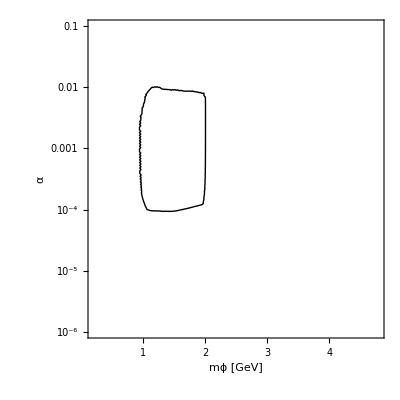

results/BelleII/BelleII_3events_kaons_newboost_newGeomInt_S-PS-V-AV_100fb.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full]]
Export["results/BelleII/BelleII_3events_kaons_newboost_newGeomInt_S-PS-V-AV_100fb.png",%]
```

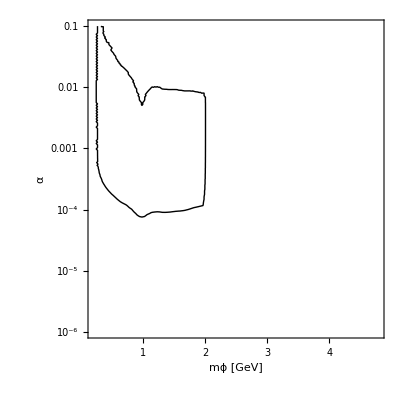

```mathematica
Show[ContourPlot[1.93 (nsbarBelleIIfullCDCkaonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full]]
(*Export["results/BelleII/BelleII_3events_pions+kaons_newboost_newGeomInt_S-PS-V-AV.png",%]*)
```

results/BelleII/BelleII_3events_pions+kaons_newboost_newGeomInt_S-PS-V-AV_100fb.png

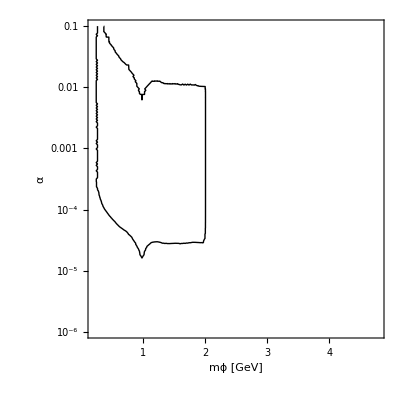

results/BelleII/BelleII_3events_pions+kaons_newboost_newGeomInt_S-PS-V-AV.png

```mathematica
Export["results/BelleII/BelleII_3events_pions+kaons_newboost_newGeomInt_S-PS-V-AV_100fb.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

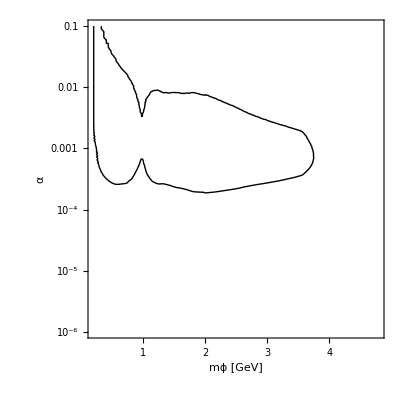

results/BelleII/BelleII_3events_muons_newboost_newGeomInt_S-PS-V-AV_100fb_100fb.png

```mathematica
Show[ContourPlot[1.93 (nsbarBelleIIfullCDCmuonK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full]]
Export["results/BelleII/BelleII_3events_muons_newboost_newGeomInt_S-PS-V-AV_100fb_100fb.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

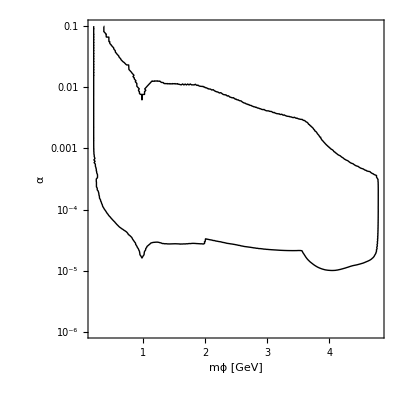

results/BelleII/BelleII_3events_pions+kaons+muons+taus_newboost_newGeomInt_S-PS-V-AV.png

```mathematica
Show[ContourPlot[1.93 (nsbarBelleIIfullCDCkaonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]+nsbarBelleIIfullCDCmuonK[m,α,0]+nsbarBelleIIfullCDCtauK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full]]
Export["results/BelleII/BelleII_3events_pions+kaons+muons+taus_newboost_newGeomInt_S-PS-V-AV.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

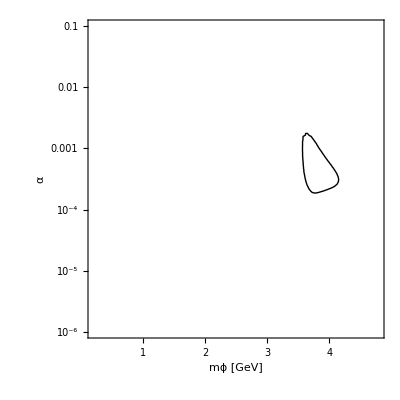

results/BelleII/BelleII_3events_taus_newboost_newGeomInt_S-PS-V-AV_100fb.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->Full]]
Export["results/BelleII/BelleII_3events_taus_newboost_newGeomInt_S-PS-V-AV_100fb.png",%]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.16519×10^7+0. ⅈ and 1.80161×10^7 for the integral and error estimates.

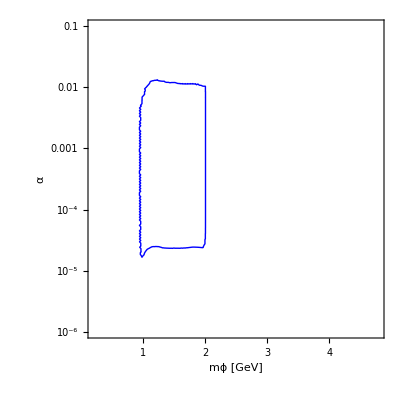

```mathematica
ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Blue},Contours->{3},PlotRange->Full]
```

```mathematica
nsbarBelleIIfullCDCkaonK[1.1,10^-4,0]
```

857.76+0. ⅈ

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,3,5},{α,8 10^-6,10^-2},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Black},ContourShading->None,Contours->{3},PlotLegends->"bkg=0",PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,3,5},{α,8 10^-6,10^-2},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Red},ContourShading->None,Contours->{3.7},PlotLegends->"bkg=1",PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,3,5},{α,8 10^-6,10^-2},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Green},ContourShading->None,Contours->{4.3},PlotLegends->"bkg=2",PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,3,5},{α,8 10^-6,10^-2},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Blue},ContourShading->None,Contours->{4.7},PlotLegends->"bkg=3",PlotRange->Full]]
Export["results/BelleII/BelleII_3events_taus-newboost_S-PS-V-AV_nonlog_bkg-vary.png",%]
```

InterpolatingFunction::dmval: Input value {3.00014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

results/BelleII/BelleII_3events_taus-newboost_S-PS-V-AV_nonlog_bkg-vary.png

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

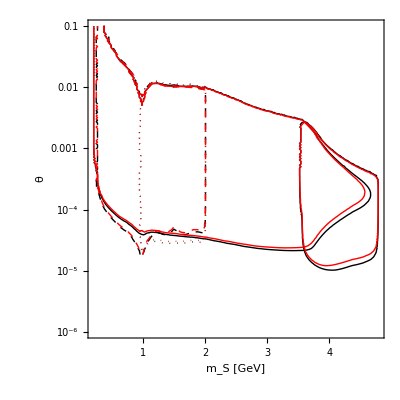

results/BelleII/BelleII_3events_muons-taus-pions-kaons_newboost_S-PS-V-AV_bkg-vary.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCmuonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{Black},Contours->{3}],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{Black,Thick},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}],ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{Black, Dotted},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCmuonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{Red},Contours->{4.7}],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{{Red,Thick}},Contours->{4.7},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{{Red, Dashed}},Contours->{4.7}],ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","θ"},ContourShading->None,ContourStyle->{{Red, Dotted}},Contours->{4.7},PlotRange->Full]]
Export["results/BelleII/BelleII_3events_muons-taus-pions-kaons_newboost_S-PS-V-AV_bkg-vary.png",%]
```

```mathematica
FindRoot[nsbarBelleIIfullCDCmuonK[4,α,0]==4.7,{α,0.001}]
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-6.86462×10^12 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (1/400+(1.45674×10^-14 Sin[θ] (1/20+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-2.22414×10^16 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (26244+(1.45674×10^-14 Sin[θ] (162+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.000759966+0. ⅈ}

```mathematica
FindRoot[nsbarBelleIIfullCDCmuonK[4,α,0]==3,{α,0.001}]
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-6.86462×10^12 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (1/400+(1.45674×10^-14 Sin[θ] (1/20+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-2.22414×10^16 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (26244+(1.45674×10^-14 Sin[θ] (162+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.000793515+0. ⅈ}

```mathematica
FindRoot[nsbarBelleIIfullCDCtauK[4,α,0]==4.7,{α,10^-5}]
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-6.86462×10^12 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (1/400+(1.45674×10^-14 Sin[θ] (1/20+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-2.22414×10^16 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (26244+(1.45674×10^-14 Sin[θ] (162+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.0000166565+0. ⅈ}

```mathematica
FindRoot[nsbarBelleIIfullCDCtauK[4,α,0]==3,{α,10^-5}]
```

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand Csc[θ] (ⅇ^(-6.86462×10^12 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (1/400+(1.45674×10^-14 Sin[θ] (1/20+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))-ⅇ^(-2.22414×10^16 Csc[θ] ((0.+0. ⅈ)+(1.80552×10^-6+0. ⅈ) Power[«2»])) (26244+(1.45674×10^-14 Sin[θ] (162+7.28372×10^-15 Power[«2»] Sin[«1»]))/((0.+0. ⅈ)+Times[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.296733,2.61807}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{α→0.0000133896+0. ⅈ}

## Getting fixed% sensitivity/significance data

```mathematica
mϕArray=Join[Range[0.2,0.37,0.03],Range[0.5,5,0.1]]
```

{0.2,0.23,0.26,0.29,0.32,0.35,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.}

```mathematica
Length[mϕArray]
```

161

```mathematica
SensitivityToFile[func_,sensitivity_,BRχArray_,mϕArray_,filename_]:=Module[{αSensitivity,αSensitivityArr,TableToPrint,BRχArrayExt},
αSensitivity[mϕ_,BRχ_]:=Re@(FindRoot[func[mϕ,α,BRχ]==sensitivity,{α,10^-3}])[[1,2]];
αSensitivityArr=Outer[αSensitivity,mϕArray,BRχArray];
BRχArrayExt=Prepend[BRχArray,0];
TableToPrint=Join[{BRχArrayExt},Transpose[Join[{mϕArray},Transpose[αSensitivityArr]]]];
Export[filename,Join[{ToString@StringForm["# m(phi)[GeV], alpha bounds BR(dark)=`1` (ignore zero in the beginnibg of next row)",BRχArray]},TableToPrint],"TSV","TextDelimiters"->None];
]
```

```mathematica
ContourplotToFile[func_,value_,BRχ_,mϕArray_,filename_]:=Module[{plot,points,joinpoints},
plot=ContourPlot[func[m,α,BRχ],{m,2mμ/.masses,mB-mK/.masses},{α,10^-5,5 10^-2},ScalingFunctions->{None,None},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->All];
points=Cases[Normal@plot,Line[pts_]->pts,Infinity];
joinpoints=Join@@points;
Export[filename,Join[{ToString@StringForm["# m(phi)[GeV], alpha bounds BR(dark)=`1`",BRχ]},joinpoints],"TSV","TextDelimiters"->None];
]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

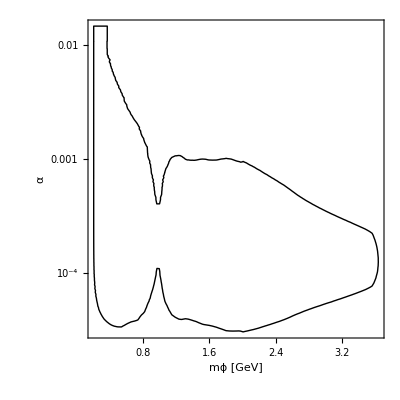

```mathematica
ContourPlot[nsbarBelleIIfullCDC[m,α,0.9],{m,2mμ/.masses,mB-mK/.masses},{α,10^-5,5 10^-2},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

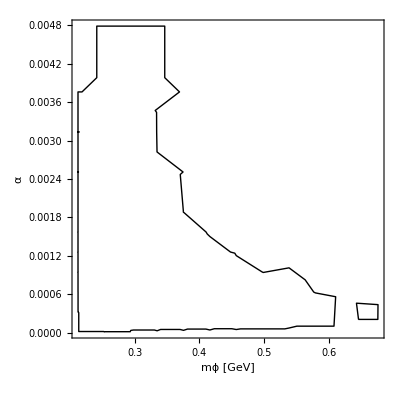

```mathematica
plot=ContourPlot[nsbarBelleIIfullCDC[m,α,0.99],{m,2mμ/.masses,mB-mK/.masses},{α,10^-5,3.5 10^-2},ScalingFunctions->{None,None},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3},PlotRange->All]
points=Cases[Normal@plot,Line[pts_]->pts,Infinity];
joinpoints=Join@@points;
```

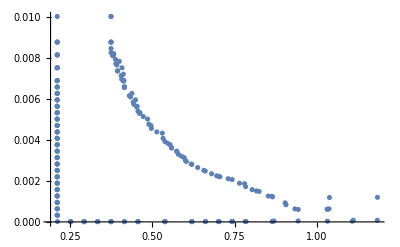

```mathematica
ListPlot[joinpoints]
```

```mathematica
Export["results/BelleII/3events_BR0.dat",Join[{ToString@StringForm["# m(phi)[GeV], alpha bounds BR(dark)=`1`",0]},joinpoints],"TSV","TextDelimiters"->None]
```

results/BelleII/3events_BR0.dat

```mathematica
ContourplotToFile[nsbarBelleIIfullCDC,3,0,mϕArray,"results/BelleII/3events_BR0.dat"]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ContourplotToFile[nsbarBelleIIfullCDC,3,0.5,mϕArray,"results/BelleII/3events_BR0.5.dat"]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ContourplotToFile[nsbarBelleIIfullCDC,3,0.9,mϕArray,"results/BelleII/3events_BR0.9.dat"]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.